# ARTIQ DATA PROCESSING

## Last Updated: 2024/09/09

```mathematica
Quit[];
```

```mathematica
(*Remove["Global`*"];
ClearInOut[];*)
```

# General

## Values

## ARTIQ Conversions

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
ftwToFrequencyMHz=(1.*^-6)*(1.*^9)/(Interpreter["HexInteger"]["FFFFFFFF"]);
```

```mathematica
(*convert 32-bit frequency tuning word (FTW) to MHz (assuming 0xFFFFFFFF is 1 GHz)*)
asfToAmplitudePCT=(1.*^2)*1./(Interpreter["HexInteger"]["3FFF"]);
```

## Fundamental

```mathematica
(*natural*)
ℏ=1.0545718*^-34;
c=2.99792458*^8;
```

```mathematica
(*statistical mechanics*)
kb=1.38064852*^-23;
```

```mathematica
(*electron units*)
me=9.10938356*^-31;
qe=1.60217662*^-19;
```

```mathematica
(*electromagnetism*)
ϵ0 = 8.8541878128*^-12;
μ0=π*4.*^-7;
```

```mathematica
(*atomic*)
amu=1.66053904*^-27;
```

## Derived

```mathematica
(*qe^2/(4 Subscript[πϵ, 0])*)
ke2=2.30707751*^-28;
```

```mathematica
(*fine structure constant*)
αfs=ke2/(ℏ*c);
```

```mathematica
(*bohr radius*)
a0=ℏ^2/(me*ke2);
```

```mathematica
(*bohr magneton*)
μB=(qe*ℏ)/(2*me);
```

```mathematica
(*debye*)
debye=(1.*^-21)/c;
```

## Units

```mathematica
(*frequency*)
{khz,mhz,ghz}={10.^3,10.^6,10.^9};
{wkhz,wmhz,wghz}=2.π*{10.^3,10.^6,10.^9};
```

```mathematica
(*time*)
{ns,μs,ms}={10.^-9,10.^-6,10.^-3};
```

```mathematica
(*distance*)
{nm,μm,mm}={10.^-9,10.^-6,10.^-3};
```

## Plotting

```mathematica
(*set plot options*)
SetOptions[Plot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Joined->False,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListLinePlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic,GridLines->Automatic];
SetOptions[ListLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];SetOptions[ListLogLogPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Joined->True,Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set signal plot options*)
SetOptions[Histogram,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ComplexListPlot,Frame-> True,FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
```

```mathematica
(*set 3d plot options*)
SetOptions[ListDensityPlot,Frame-> True, FrameTicksStyle-> Directive[Black,15],Background->White,ImageSize->Large,GridLines->Automatic];
SetOptions[ListPlot3D,Background->None,ImageSize->Large];
```

## Evaluations

```mathematica
(*scde2={
Off[General::munfl],
Off[FindRoot::lstol],
Off[FindFit::cvmit],
Off[FindFit::sszero],
Off[FindFit::nrjnum],
Off[NonlinearModelFit::cvmit],
Off[NonlinearModelFit::sszero],
Off[Power::infy],
Off[Infinity::indet],
Off[FittedModel::constr]
};*)
```

```mathematica
(*Evaluate[#]&/@scde2*)
```

```mathematica
(*scde={
General::munfl,
FindRoot::lstol,
FindFit::cvmit,
FindFit::sszero,
FindFit::nrjnum,
NonlinearModelFit::cvmit,
NonlinearModelFit::sszero,
Power::infy,
Infinity::indet,
FittedModel::constr
};*)
```

```mathematica
(*Off[#]&/@scde*)
```

```mathematica
(*turn upsetting things off*)
ParallelEvaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
Evaluate[
Off[General::munfl];
Off[FindRoot::lstol];
Off[FindFit::cvmit];
Off[FindFit::sszero];
Off[FindFit::nrjnum];
Off[NonlinearModelFit::cvmit];
Off[NonlinearModelFit::sszero];
Off[Power::infy];
Off[Infinity::indet];
Off[FittedModel::constr];
Off[InterpolatingFunction::dmval];
];
```

## Functions

## General

```mathematica
(*play sound when finished*)
Done[type_:"email",msg_:""]:=With[{soundDJ=Play[Sin[600*π*t],{t,0,0.6}]},
Switch[type,
"text",SendMessage["SMS",msg],
"email",SendMail[<|"To"->"claytonho@g.ucla.edu","Subject"->ToString[$MachineName],"From"->"claytonho@physics.ucla.edu","Server"->"smtp.physics.ucla.edu","EncryptionProtocol"->"SSL","PortNumber"->465,"UserName"->"claytonho@physics.ucla.edu","Body"->msg,"Password"->"I2Ic1zIS2R"|>],"none",EmitSound[soundDJ]
];
];
```

## Phonon Conversion

```mathematica
coherentX0="0\t9.99968345065521e-05\t0.000399949359050543\t0.000899743688795304\t0.00159919018917467\t0.00249802373567682\t0.00359590407662662\t0.00489241629804741\t0.00638707138943964\t0.00807930690905264\t0.00996848774698177\t0.0120539069841832\t0.0143347868452619\t0.0168102797426638\t0.0194794694096749\t0.0223413721194334\t0.0253949379869404\t0.0286390523508750\t0.0320725372318338\t0.0356941528634366\t0.0395025992925868\t0.0434965180450157\t0.0476744938521131\t0.0520350564349007\t0.0565766823409077\t0.0612977968295938\t0.0661967758018701\t0.0712719477691913\t0.0765215958576296\t0.0819439598422616\t0.0875372382071775\t0.0932995902263676\t0.0992291380607130\t0.105323968866310\t0.111582136909319\t0.118001665682565\t0.124580550019086\t0.131316758197884\t0.138208234037120\t0.145252898970045\t0.152448654098991\t0.159793382222768\t0.167284949832890\t0.174921209074062\t0.182699999664427\t0.190619150771128\t0.198676482836768\t0.206869809352429\t0.215196938572920\t0.223655675170015\t0.232243821819463\t0.240959180717564\t0.249799555023207\t0.258762750221224\t0.267846575402984\t0.277048844460143\t0.286367377187489\t0.295800000290804\t0.305344548295672\t0.314998864353126\t0.324760800938008\t0.334628220435874\t0.344598995614207\t0.354671009973656\t0.364842157974930\t0.375110345136883\t0.385473488001222\t0.395929513959161\t0.406476360935198\t0.417111976923057\t0.427834319368674\t0.438641354394938\t0.449531055862707\t0.460501404262433\t0.471550385430509\t0.482675989084237\t0.493876207169105\t0.505149032011798\t0.516492454272143\t0.527904460686948\t0.539383031598436\t0.550926138259732\t0.562531739909640\t0.574197780608683\t0.585922185828196\t0.597702858784029\t0.609537676506275\t0.621424485636251\t0.633361097941900\t0.645345285542670\t0.657374775834950\t0.669447246109191\t0.681560317849959\t0.693711550710419\t0.705898436153020\t0.718118390748662\t0.730368749127130\t0.742646756572379\t0.754949561257081\t0.767274206112027\t0.779617620327223\t0.791976610483122";
coherentX0=Internal`StringToMReal/@StringSplit[coherentX0,"\t"];
```

```mathematica
coherentY0="0\t0.000100000000000000\t0.000400000000000000\t0.000900000000000000\t0.00160000000000000\t0.00250000000000000\t0.00360000000000000\t0.00490000000000000\t0.00640000000000000\t0.00810000000000000\t0.0100000000000000\t0.0121000000000000\t0.0144000000000000\t0.0169000000000000\t0.0196000000000000\t0.0225000000000000\t0.0256000000000000\t0.0289000000000000\t0.0324000000000000\t0.0361000000000000\t0.0400000000000000\t0.0441000000000000\t0.0484000000000000\t0.0529000000000000\t0.0576000000000000\t0.0625000000000000\t0.0676000000000000\t0.0729000000000000\t0.0784000000000000\t0.0841000000000000\t0.0900000000000000\t0.0961000000000000\t0.102400000000000\t0.108900000000000\t0.115600000000000\t0.122500000000000\t0.129600000000000\t0.136900000000000\t0.144400000000000\t0.152100000000000\t0.160000000000000\t0.168100000000000\t0.176400000000000\t0.184900000000000\t0.193600000000000\t0.202500000000000\t0.211600000000000\t0.220900000000000\t0.230400000000000\t0.240100000000000\t0.250000000000000\t0.260100000000000\t0.270400000000000\t0.280900000000000\t0.291600000000000\t0.302500000000000\t0.313600000000000\t0.324900000000000\t0.336400000000000\t0.348100000000000\t0.360000000000000\t0.372100000000000\t0.384400000000000\t0.396900000000000\t0.409600000000000\t0.422500000000000\t0.435600000000000\t0.448900000000000\t0.462400000000000\t0.476100000000000\t0.490000000000000\t0.504100000000000\t0.518400000000000\t0.532900000000000\t0.547600000000000\t0.562500000000000\t0.577600000000000\t0.592900000000000\t0.608400000000000\t0.624100000000000\t0.640000000000000\t0.656100000000000\t0.672400000000000\t0.688900000000000\t0.705600000000000\t0.722500000000000\t0.739600000000000\t0.756900000000000\t0.774400000000000\t0.792100000000000\t0.810000000000000\t0.828100000000000\t0.846400000000000\t0.864900000000000\t0.883600000000000\t0.902500000000000\t0.921600000000000\t0.940900000000000\t0.960400000000000\t0.980100000000000\t1\t1.02010000000000";
coherentY0=Internal`StringToMReal/@StringSplit[coherentY0,"\t"];
```

```mathematica
(*CoherentC=Interpolation[Transpose[{coherentX0,coherentY0}]];*)
CoherentCFunc=Interpolation[Transpose[{coherentX0,coherentY0}]];
CoherentC[x_]:=CoherentCFunc[#]&[Clip[x,{0.,0.8}]];
```

## Dataset Processing

### Import

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQ[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
parameterList=Join@@{
Import[filenameDJ,{"Attributes","/arguments"}],
Import[filenameDJ,{"Attributes","/parameters"}]
};

Return[{datasetRaw,parameterList}];
];
```

### Processing

```mathematica
(*threshold counts into s-state vs d-state probability*)
Options[ThresholdCounts]={
"Threshold"->-1
};
ThresholdCounts[dataset_List,countsColumn_Integer,OptionsPattern[]]:=Module[
{
results=dataset,

(*find state discrimination threshold*)
countThreshold=If[
OptionValue["Threshold"]!=-1,
OptionValue["Threshold"],
FindThreshold[dataset[[;;,countsColumn]],Method->"MinimumError"]
]
},

(*directly threshold counts into D-state probability*)
results[[;;,countsColumn]]=1.-UnitStep[results[[;;,countsColumn]]-countThreshold];
(*Print[countThreshold];*)
Return[results];
];
```

```mathematica
(*group the data as desired, then take the mean of whatever remains*)
CollateData[dataset_List,groupColumnList_List]:=GroupBy[dataset,
Table[
With[{i=i},#[[i]]&],
{i,groupColumnList}
],
N[Mean[#]]&
]//KeySort;
```

### Analysis

```mathematica
(*sinc-squared function for spetroscopy fitting*)
SincModel[α_,β_,δ_,t_,x_]:=α*Sinc[(π*t)*((x-β)*khz)+0.0000000001]^2+δ;
```

```mathematica
(*fit sinc and return params with error and confidence intervals*)
FitSinc[dataset_List,timeSinc:(_Integer|_Real)]:=Module[
{
guessMax=dataset[[First@Ordering[dataset[[;;,2]],-1]]],
guessOffset=Mean[{Median[dataset[[;;,2]]],Mean[dataset[[;;,2]]]}],
guessParamList,

α,β,γ,δ,x,
sincConstraints,
sincModel,

fitResult
},

(*create sinc model*)
sincModel=α*Sinc[(π*timeSinc)*((x-β)*khz)+0.00000001]^2+δ;

(*guess sinc fit parameters*)
guessParamList={
(guessMax[[2]]-guessOffset),(*rabi frequency*)
guessMax[[1]],(*resonance frequency*)
guessOffset (*background offset*)
};

(*constrain search range for parameters*)
sincConstraints={
(*α>0,α<αRSBguess*3,*)
(*β>0.975*βRSBguess,β<1.025*βRSBguess*)
δ>0
};

(*fit sinc model - nonlinearmodelfit to extract extra fit information*)
fitResult=NonlinearModelFit[
dataset,
Join[{sincModel,sincConstraints}],
Transpose[{{α,β,δ},guessParamList}],
x,
MaxIterations->10^4
];

(*todo: return parameters and their error*)
Return[fitResult["ParameterConfidenceIntervalTableEntries"]];
];
```

## Batch Processing

```mathematica
(*(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS[filedir_,filekey_]:=Module[
{
(*actual data*)
(*datafile=ImportDatasetARTIQ[filedir,ToString[filekey]],*)
datafile,
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*import dataset*)
datafile=ImportDatasetARTIQ[filedir,ToString[filekey]];

(*extract heating time from parameter list*)
heatingTimeSeconds=datafile[[2]]["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[datafile[[1]]]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->datafile[[2]],
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datafile,datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
(*Remove[datafile];*)
ClearSystemCache[];

(*return dataset*)
Return[results];
];*)
```

```mathematica
(*batch process eggs data for calibration (i.e. w/ sideband sweep), returning relevant values*)
ProcessDatasetEGGS2[dataset_List,parameterList_Association]:=Module[
{
(*actual data*)
heatingTimeSeconds,
results=<||>,

(*processing*)
datasetProcessed,
rsbData,bsbData,

(*analysis*)
sidebandRatio,phononData,
rsbFitParams,phononFitParams
},

(*extract heating time from parameter list*)
heatingTimeSeconds=parameterList["time_eggs_heating_ms"]*ms;

(*convert dataset into correct units*)
datasetProcessed=Transpose[
Transpose[dataset]*
{ftwToFrequencyMHz,1.,1.*^-6,1.*^-3}
];
(*threshold ion fluorescence counts into D-state probability*)
datasetProcessed=ThresholdCounts[datasetProcessed,2];
(*collate data by rsb/bsb and sideband frequency*)
datasetProcessed=CollateData[datasetProcessed,{1,4}];

(*separate rsb/bsb data as 2-D datasetss*)
{rsbData,bsbData}=SortBy[
Values[#][[;;,{4,2}]],
First
]&/@Values[datasetProcessed];
(*fit rsb*)
rsbFitParams=FitSinc[rsbData,heatingTimeSeconds];

(*add intermediate results*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"ParameterList"->parameterList,
"BSBData"->bsbData,
"RSBData"->rsbData,
"RSBFitParams"->rsbFitParams,
"SBPlot"->Show[
ListPlot[
{rsbData,bsbData}
],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@rsbFitParams[[;;,1]],
{δ,rsbData[[1,1]],rsbData[[-1,1]]}
]]
}];

(*subtract background and create rsb/bsb ratio array*)
sidebandRatio=Transpose[{
rsbData[[;;,1]],
Ramp[(rsbData[[;;,2]]-rsbFitParams[[3,1]])/(bsbData[[;;,2]]-rsbFitParams[[3,1]])]
}];
(*convert to phonon number assuming coherent state*)
phononData=sidebandRatio;
phononData[[;;,2]]=CoherentC[sidebandRatio[[;;,2]]];
(*fit sinc to phonon number*)
phononFitParams=FitSinc[sidebandRatio,heatingTimeSeconds];

(*add intermediate computations to output*)
AssociateTo[results,
(*todo: plot style, axes units*)
{
"SidebandRatioData"->sidebandRatio,
"PhononData"->phononData,
"PhononFitParams"->phononFitParams,
"PhononPlot"->Show[
ListPlot[phononData],
Plot[
SincModel[##,heatingTimeSeconds,δ]&@@phononFitParams[[;;,1]],
{δ,phononData[[1,1]],phononData[[-1,1]]}
]]
}];


(*clean up mess*)
Remove[datasetProcessed,rsbData,bsbData,sidebandRatio,phononData,rsbFitParams,phononFitParams];
ClearSystemCache[];

(*return dataset*)
Return[results];
];
```

# User Input

## Parameters

```mathematica
(*top level directory for imports*)
directoryString="Z:\\motion\\Data\\2024-12\\2024-12-01";
```

## Validate User Input

```mathematica
(*check input directory exists*)
If[!DirectoryQ[directoryString],
MessageDialog["Failure :(\nError: Import directory not found ("<>directoryString<>")."];
FrontEndTokenExecute["EvaluatorAbort"];
];
```

# Run

## tmp batch

```mathematica
directoryString="Z:\\motion\\Data\\2023-10-04";
```

```mathematica
ridArr=Join[
Range[36085,36089]
];
datafileArr=ImportDatasetARTIQ[directoryString,#]&/@ridArr;
```

$Aborted

```mathematica
xArr=#[[2]]["phase_antisqueeze_turns_list"][[1]]&/@datafileArr;
```

```mathematica
th0=ThresholdCounts[#[[1]],2]&/@datafileArr;
th1=CollateData[#,{1}]&/@th0;
```

```mathematica
freqCenter=Mean[Mean[Values[#[[;;,1]]]]&/@th1];
rsbYArr=#[[1]]&/@th1;rsbYArr=rsbYArr[[;;,2]];
bsbYArr=#[[2]]&/@th1;bsbYArr=bsbYArr[[;;,2]];
```

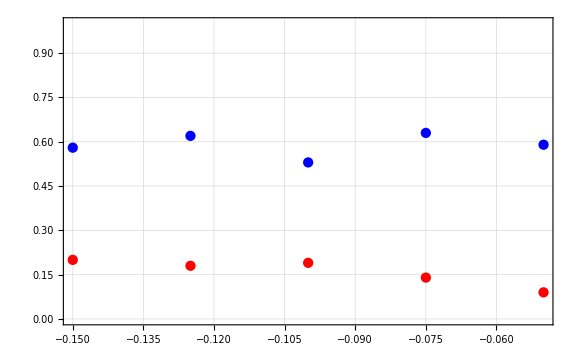

```mathematica
ListPlot[
{
Transpose[{xArr,rsbYArr}],
Transpose[{xArr,bsbYArr}]
},
PlotStyle->{Red,Blue},
PlotRange->{Automatic,{0,1}}
]
```

## ISA single point wsec/phase sweep

```mathematica
rid=88836;
phaseIdx=6;
```

## Import & Examine

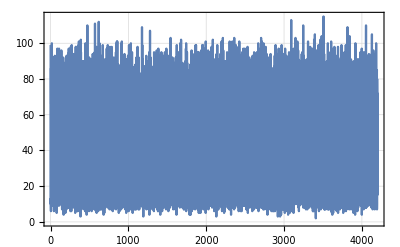
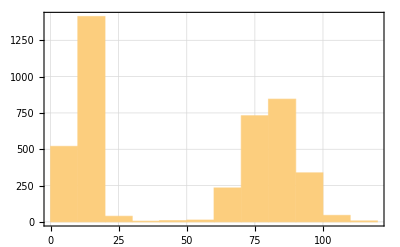
{-Graphics-,-Graphics-,(Missing[KeyAbsent,att_squeeze_db]
Missing[KeyAbsent,phase_antisqueeze_turns_list]
Missing[KeyAbsent,enable_antisqueezing])}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["phase_antisqueeze_turns_list"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

```mathematica
dataset[[;;5]]//MatrixForm
```

(4.38331×10^8 | 99. | 5.175×10^8 | 1.14198×10^6 | 0. | 0.8 | 138539.
4.38331×10^8 | 10. | 5.175×10^8 | 1.14198×10^6 | 0. | 0.7 | 138539.
4.38331×10^8 | 13. | 5.175×10^8 | 1.14198×10^6 | 0. | 0.6 | 138539.
4.38331×10^8 | 9. | 5.175×10^8 | 1.14198×10^6 | 0. | 0.85 | 138539.
4.38331×10^8 | 6. | 5.175×10^8 | 1.14198×10^6 | 0. | 0.1 | 138539.)

## Process

```mathematica
(*get parameters*)
phaseRSB=dataset[[;;,5]]//Mean;
phaseCH1=dataset[[;;,6]]//Mean;
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,phaseIdx,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=(dsB[[;;,2]]+1.*^-6);
```

## Fit

```mathematica
(*guess values*)
{xMax,yMax}=dsN[[First@Ordering[dsN[[;;,2]],-1]]];
cMean=Mean[dsN[[;;,2]]];
(*phaseSPSweepGuess={
yMax,(*α*)
xMax(*β*)
}*)
phaseSPSweepGuess={
yMax,(*α*)
xMax,(*β*)
cMean(*γ*)
}
```

{0.337662,0.55,0.206744}

```mathematica
phaseSPSweepModel=α*Cos[2.π*(x-β)]+γ;
```

```mathematica
phaseSPSweepConstraints={
0.<α<1.5,
0.<β<1
(*0.<δ<0.1*)
};
```

```mathematica
phaseSPSweepFit=NonlinearModelFit[
dsN,
Join[{phaseSPSweepModel,phaseSPSweepConstraints}],
Transpose[{{α,β,γ},phaseSPSweepGuess}],
x
];
```

```mathematica
phaseSPFitParams=Style[
phaseSPSweepFit["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot raw data*)
dataPointsPlot=ListPlot[
{dsN},
PlotRange->{Automatic,Automatic},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Phase (turns)",{Black,Directive[15]}],
Style["ISA Phase Sweep (Single Point)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{(*Red,Blue,*)Black}
];
```

```mathematica
(*plot fitted result*)
phaseSPSweepFitPlot=Plot[
phaseSPSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
];
```

## Show

```mathematica
{
phaseRSB,
phaseCH1
}
```

{0.,0.5}

| Estimate | Standard Error | Confidence Interval
α | 0.0382309 | 0.0159065 | {0.00481257,0.0716493}
β | 0.462695 | 0.0689606 | {0.317814,0.607576}
γ | 0.208515 | 0.0114828 | {0.18439,0.232639}

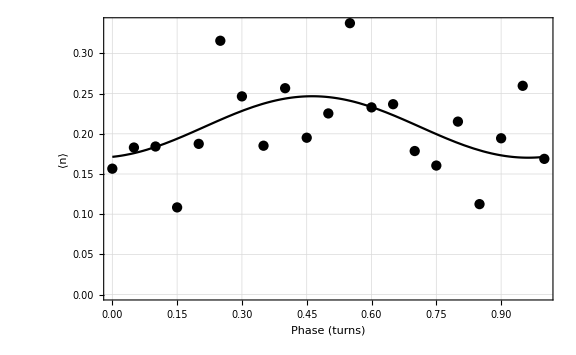

```mathematica
phaseSPFitParams
Show[
dataPointsPlot,
phaseSPSweepFitPlot
]
```

```mathematica
1-0.797613
```

0.202387

## squeeze freq sweep

```mathematica
rid=52354;
```

### Import

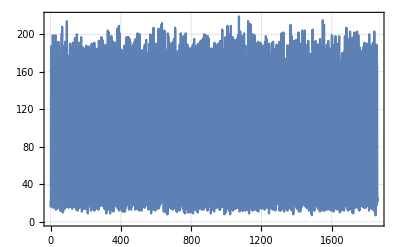
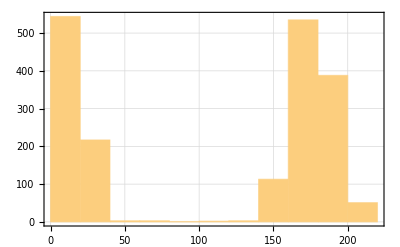
{-Graphics-,-Graphics-,(24.5
{10.}
{0.33017}
{1000.}
1
1)}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["time_delay_us_list"],
parameters["enable_squeezing"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=dsB[[;;,2]];
```

### Fit

```mathematica
(*guess values*)
sqFreqSweepGuess={
1.-#[[2]],(*α*)
#[[1]],(*β*)
1000./(First@parameters["time_delay_us_list"]),(*γ*)
1.0(*δ*)
}&[dsN[[First@Ordering[dsN[[;;,2]],1]]]]
```

{0.913043,753.135,1.,1.}

```mathematica
sqFreqSweepModel=-α*Exp[-(f-β)^2./γ]+δ;
sqFreqSweepConstraints={
0.<α<1.,
740.<β<760.,
0.<γ<10.,
0.1<δ<1.3
};
```

```mathematica
sqFreqSweepFit=NonlinearModelFit[
dsN,
Join[{sqFreqSweepModel,sqFreqSweepConstraints}],
Transpose[{{α,β,γ,δ},sqFreqSweepGuess}],
f
];
```

### Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,dsR,
dsB,dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
],
Show[
ListPlot[
{
dsN,
dsN
},
(*PlotRange->{Automatic,{0,1}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True},
PlotStyle->{
{Black},
{Black,Dashed}
}
],
Plot[
sqFreqSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
]
]
};
```

### Show

| Estimate | Standard Error | Confidence Interval
α | 0.777733 | 6.64198 | {-12.8505,14.406}
β | 752.446 | 0.409877 | {751.605,753.287}
γ | 6.93343 | 71.5913 | {-139.96,153.827}
δ | 1.3 | 6.69341 | {-12.4338,15.0337}

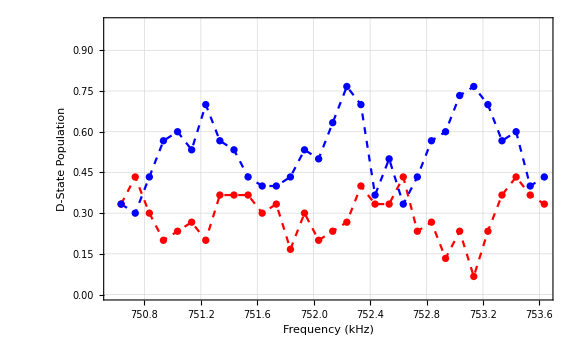
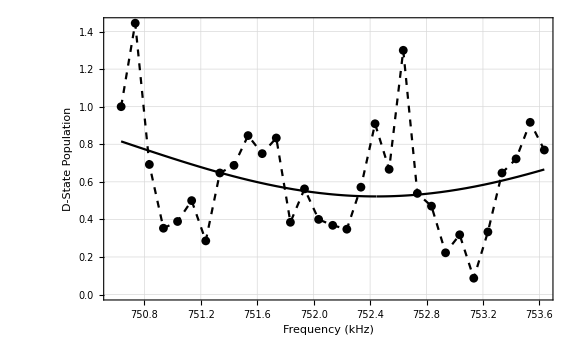

```mathematica
Style[sqFreqSweepFit["ParameterConfidenceIntervalTable"],{Background->White}]
summaryFigure
```

## squeeze freq sweep (sinc fit)

```mathematica
rid=62381;
```

## Import

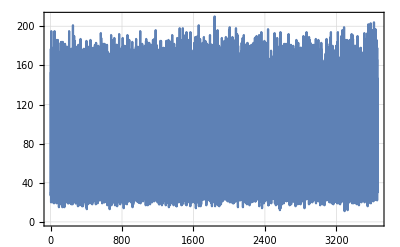
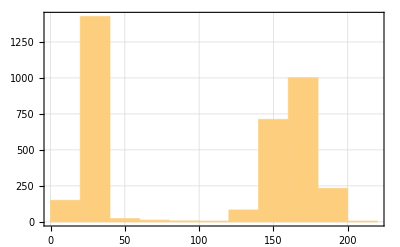
{-Graphics-,-Graphics-,(31.5
{1000.}
{0.}
{5.}
1
0)}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["time_delay_us_list"],
parameters["enable_squeezing"],
parameters["enable_antisqueezing"]
}]
}&[dataset[[;;,2]]]
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*process ratio*)
dsN=dsR;
dsN[[;;,2]]/=dsB[[;;,2]];
```

## Fit

```mathematica
(*guess values*)
sqFreqSweepGuess={
1.-#[[2]],(*α*)
#[[1]],(*β*)
2.*π*1.*^-6*(First@parameters["time_squeeze_us_list"]),(*γ*)
1.0(*δ*)
}&[dsN[[First@Ordering[dsN[[;;,2]],1]]]]
```

{1.,1417.2,0.00628319,1.}

```mathematica
sqFreqSweepModel=α*Sinc[γ*(f-β)+0.0001]^2.+δ;
```

```mathematica
sqFreqSweepConstraints={
0.<α<1.5,
1410.<β<1430.,
(*0.<γ<10.,*)
0.<δ<0.1
};
```

```mathematica
sqFreqSweepFit=NonlinearModelFit[
dsN,
Join[{sqFreqSweepModel,sqFreqSweepConstraints}],
Transpose[{{α,β,γ,δ},sqFreqSweepGuess}],
f
];
```

## Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,dsR,
dsB,dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
],
Show[
ListPlot[
{
dsN,
dsN
},
(*PlotRange->{Automatic,{0,1}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (kHz)",{Black,Directive[15]}],
(*Style["Motional Ramsey (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]*)
Style["EGGS - DDS\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
Joined->{False,True},
PlotStyle->{
{Black},
{Black,Dashed}
}
],
Plot[
sqFreqSweepFit[ω],
{ω,dsN[[1,1]],dsN[[-1,1]]},
PlotStyle->{Black}
]
]
};
```

## Show

| Estimate | Standard Error | Confidence Interval
α | 0.284009 | 0.024187 | {0.235576,0.332443}
β | 1420.45 | 0.0432578 | {1420.37,1420.54}
γ | 2.49562 | 0.221137 | {2.0528,2.93844}
δ | 0.0162314 | 0.0091349 | {-0.0020609,0.0345237}

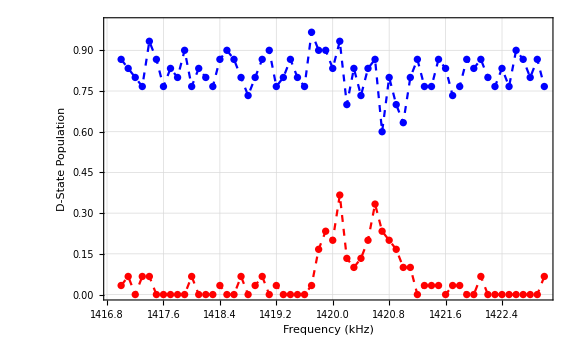
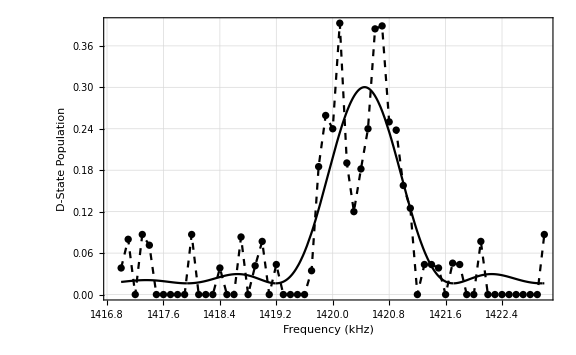

```mathematica
Style[sqFreqSweepFit["ParameterConfidenceIntervalTable"],{Background->White}]
summaryFigure
```

## ramsey phase sweep

```mathematica
rid=89388;
sweepIDX=3;
```

### Import

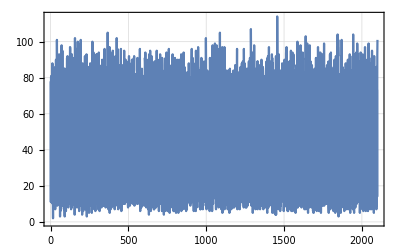
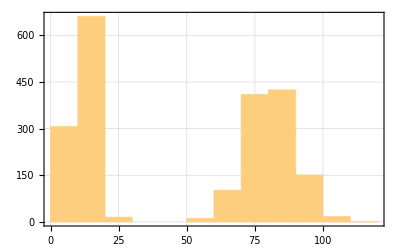

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

### Process

```mathematica
(*get parameters*)
timeDelayUS=parameters["time_ramsey_delay_us"];
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,sweepIDX,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.(*1./(2.^16.-1.)*),1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

Thread::tdlen: Objects of unequal length in {}/{0.466667} cannot be combined.

### Fit

```mathematica
fitfunc=α*Sin[(1.*π)*(ϕ-γ)]^2.+β;
```

```mathematica
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc,
α>0.,β>0.,0.5>=γ>=-0.5
},
{
{α,0.8},
{γ,0.},
{β,0.}
},
ϕ
];
]
```

NonlinearModelFit::fitd: First argument {} in NonlinearModelFit is not a list or a rectangular array.

{0.0366059,Null}

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

### Plot

```mathematica
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Plot::plln: Limiting value {}⟦1,1⟧ in {ϕ,{}⟦1,1⟧,{}⟦-1,1⟧} is not a machine-sized real number.

```mathematica
summaryFigure={
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[timeDelayUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Black}
],
fitPlot
],
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[timeDelayUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue,Black}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
]
};
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

ListPlot::lpn: {{},{{0.,0.466667}}} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

### Show

0.587302

| Estimate | Standard Error | Confidence Interval
α | 0.550993 | 0.0620044 | {0.420727,0.681259}
γ | 0.352415 | 0.0176835 | {0.315264,0.389567}
β | 2.00661×10^-7 | 0.0385672 | {-0.0810265,0.0810269}

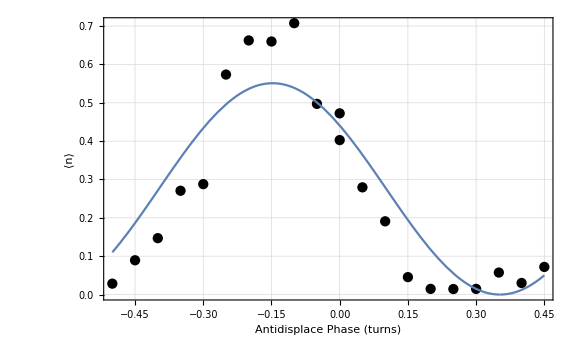
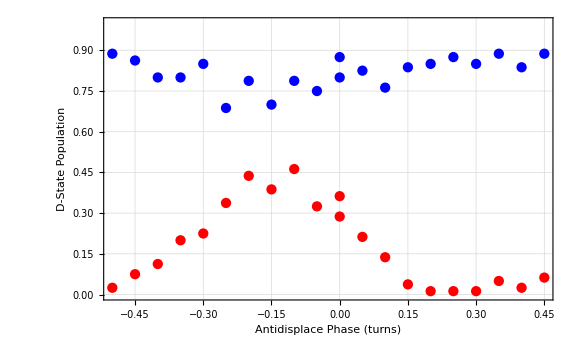

```mathematica
Max[dsRatio[[;;,2]]]
fitParams
summaryFigure
```

## ramsey fit

```mathematica
rid=85291;
ϕ0=0.;
```

### Import

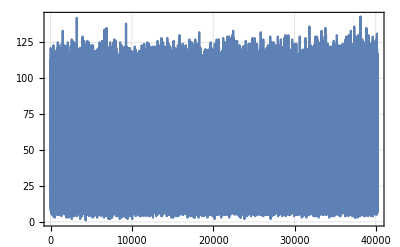
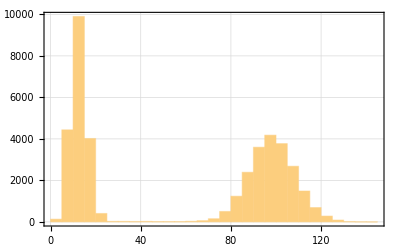

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
(*extract important parameters*)
timeRamseyUS=parameters["time_ramsey_delay_us"];
timeDisplaceUS=parameters["time_eggs_heating_us"];
timePulseshapeUS=parameters["time_pulse_shape_rolloff_us"]*parameters["enable_pulse_shaping"];
phaseRamseyTurns=First@parameters["phase_ramsey_anti_turns_list"];

(*calculate approximate displacement time*)
timeEGGSus=timeDisplaceUS+timePulseshapeUS*(2.*0.5);
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,4,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,(*1./(2.^16.-1.)*)1.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*phase unwrap*)
(*dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];*)
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

### Fit

#### Complete Ramsey Fit

```mathematica
(*displace ramsey fit function*)
fitfunc=4. Ω^2. τ^2. Sinc[(2.*π)*((x-β)*τ)/2.+1.*^-5]^2. Sin[(2.*π)*(((x-β)*(T+τ))/2.+ϕ)]^2.+δ;
(*set fixed values*)
fitfunc=fitfunc/.{
τ->(timeEGGSus*1.*^-6),
T->(timeRamseyUS*1.*^-6),
β->Mean[dsN[[;;,1]]]
(*ϕ->0.*)
};
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{Ω,1.*^4},
{β,Mean[dsN[[;;,1]]]},
{τ,timeEGGSus*1.*^-6},
{T,timeRamseyUS*1.*^-6},
{δ,Mean[dsN[[;;,2]]]},
{ϕ,0.}
},
x
];
]
```

{0.0056621,Null}

#### General Sine Fit

```mathematica
(*(*general sine fit*)
fitfunc=α*Sin[(1.*π)*(T)*(x-β)(*+ϕ*)]^2.+δ;
(*fitfunc=α*Sin[(1.*π)*(T)*(x-β)]^2.+δ;*)

(*set fixed values*)
fitfunc=fitfunc/.{
(*T->(timeRamseyUS+timeEGGSus)*1.*^-6,*)
(*β->Mean[dsN[[;;,1]]]*)
};*)
```

```mathematica
(*(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{α,0.7},
{β,Mean[dsN[[;;,1]]]},
{T,(timeRamseyUS+timeEGGSus)*1.*^-6},
{δ,Min[dsN[[;;,2]]]}
(*{ϕ,0.}*)
},
x
];
]*)
```

#### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

### Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
dsN,
dsN
},
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
],
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black}
]
};
```

### Show

0.

| Estimate | Standard Error | Confidence Interval
Ω | 3728.51 | 141.679 | {3449.09,4007.93}
β | 1.28077×10^6 | 2.88576×10^-12 | {1.28077×10^6,1.28077×10^6}
τ | 0.00006 | 0. | {0.00006,0.00006}
T | 0.0005 | 0. | {0.0005,0.0005}
δ | 0.074689 | 0.00686279 | {0.0611541,0.0882238}
ϕ | 0.176431 | 0.00668086 | {0.163255,0.189607}

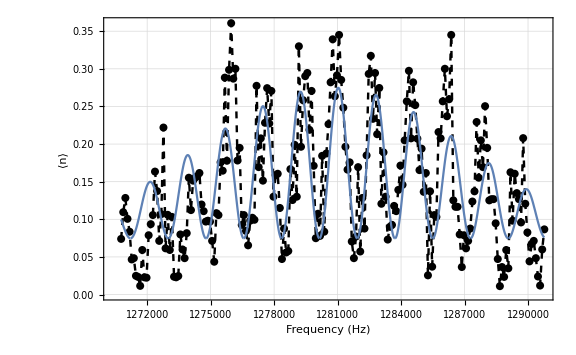
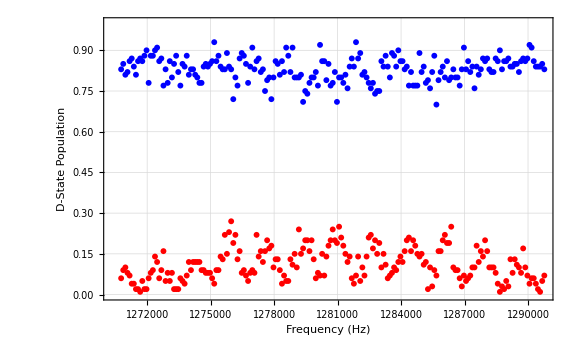

```mathematica
phaseRamseyTurns
fitParams
summaryFigure
```

```mathematica
{1000./#/20.,1000./#*2.5}&[500]
```

{0.1,5.}

## 729nm ramsey freq sweep

```mathematica
rid=89462;
ϕ0=0.;
phaseIdx=1;
```

## Import

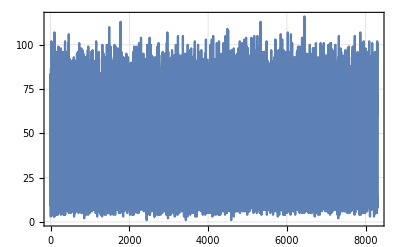
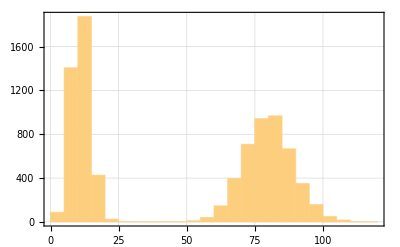
{(4.3585×10^8 | 84. | 3.×10^6 | 0.
4.3585×10^8 | 82. | 3.×10^6 | 0.
4.3585×10^8 | 10. | 3.×10^6 | 0.),-Graphics-,-Graphics-}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

```mathematica
(*extract important parameters*)
(*{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}*)
timeRamseyUS=First@parameters["time_delay_us_list"];
timePulseUS=parameters["time_pulse_us"];
phaseRamseyTurns=First@parameters["phase_ramsey_turns_list"];
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseIdx,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

## Fit

### Complete Ramsey Fit

```mathematica
(*(*displace ramsey fit function*)
fitfunc=4. Ω^2. τ^2. Sinc[(2.*π)*((x-β)*τ)/2.+1.*^-5]^2. Sin[(2.*π)*(((x-β)*(T+τ))/2.+ϕ)]^2.+δ;
(*set fixed values*)
fitfunc=fitfunc/.{
τ->(timePulseUS(**1.*^-6*)),
T->(timeRamseyUS(**1.*^-6*)),
β->Mean[datasetProcessed[[;;,1]]]
(*ϕ->0.*)
};*)
```

```mathematica
(*(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{Ω,1.*^4},
{β,Mean[datasetProcessed[[;;,1]]]},
{τ,timePulseUS(**1.*^-6*)},
{T,timeRamseyUS(**1.*^-6*)},
{δ,Mean[datasetProcessed[[;;,2]]]},
{ϕ,0.}
},
x
];
]*)
```

### General Sine Fit

```mathematica
(*general sine fit*)
fitfunc=α*Cos[(2.*π)*(T)*(x-β)+ϕ]^2.+δ;

(*set fixed values*)
fitfunc=fitfunc/.{
T->(timeRamseyUS+timePulseUS)(**1.*^-6*),
ϕ->(2.*π)*phaseRamseyTurns
}
```

δ+α Cos[0.+18905.4 (x-β)]^2.

```mathematica
(*guess initial values*)
guessα=1.0*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]]);
guessβ=Mean[datasetProcessed[[;;,1]]];
guessT=(timeRamseyUS+timePulseUS)(**1.*^-6*);
guessδ=Mean[datasetProcessed[[;;,2]]];
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
{
fitfunc
},
Transpose[{
{α,β,T,δ},
{guessα,guessβ,guessT,guessδ}
}],
x
];
]
```

{0.0049044,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["P_(S - 1/2)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["729nm Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

```mathematica
101.47918463011267
```

101.479

0.

| Estimate | Standard Error | Confidence Interval
α | 0.103828 | 0.0140966 | {0.0757696,0.131887}
β | 101.479 | 3.58975×10^-6 | {101.479,101.479}
T | 3008.88 | 0. | {3008.88,3008.88}
δ | 0.408886 | 0.00863683 | {0.391694,0.426077}

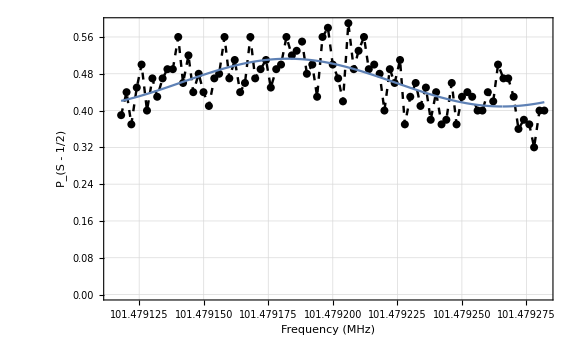

```mathematica
phaseRamseyTurns
fitParams
summaryFigure
```

```mathematica
{0.005,5.*^-5}*100./1000.
```

{0.0005,5.×10^-6}

## 729nm ramsey phase sweep

```mathematica
rid=89388;
ϕ0=0.;
phaseIdx=4;
```

## Import

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
dataset[[;;3,;;]]//MatrixForm,
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
}&[dataset[[;;,2]]]
```

{(4.38648×10^8 | 78. | 99999. | 22938.
4.38648×10^8 | 11. | 99999. | 42598.
4.38648×10^8 | 80. | 99999. | 26214.),-Graphics-,-Graphics-}

```mathematica
(*extract important parameters*)
(*{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}*)
timeRamseyUS=First@parameters["time_delay_us_list"];
timePulseUS=parameters["time_pulse_us"];
phaseRamseyTurns=First@parameters["phase_ramsey_turns_list"];
```

## Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{phaseIdx,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{1./(2^16-1.),1.}];
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

```mathematica
(*phase unwrap & sort*)
datasetProcessed[[;;,1]]=Mod[datasetProcessed[[;;,1]],1,-0.5];
datasetProcessed=SortBy[datasetProcessed,First];
```

## Fit

### General Sine Fit

```mathematica
(*general sine fit*)
fitfunc=α*Cos[(2.*π)*(x-β)]^2.+δ;
```

```mathematica
(*guess initial values*)
guessα=1.0*(Max[datasetProcessed[[;;,2]]]-Min[datasetProcessed[[;;,2]]]);
guessβ=Mean[datasetProcessed[[;;,1]]];
guessδ=Mean[datasetProcessed[[;;,2]]];
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
datasetProcessed,
{
fitfunc
},
Transpose[{
{α,β,δ},
{guessα,guessβ,guessδ}
}],
x
];
]
```

{0.0053298,Null}

### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

## Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[x],
{x,datasetProcessed[[1,1]],datasetProcessed[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
Show[
ListPlot[
{
datasetProcessed,
datasetProcessed
},
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["P_(S - 1/2)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["729nm Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

## Show

0.4

| Estimate | Standard Error | Confidence Interval
α | -0.796163 | 0.0300542 | {-0.859572,-0.732754}
β | -0.0635156 | 0.00300399 | {-0.0698535,-0.0571778}
δ | 0.878587 | 0.0184046 | {0.839757,0.917417}

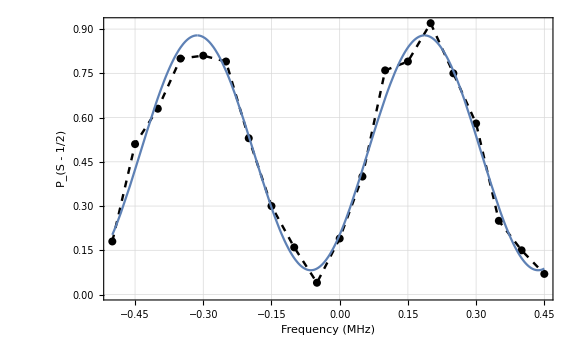

```mathematica
phaseRamseyTurns
fitParams
summaryFigure
```

```mathematica
{0.005,5.*^-5}*250./100.
```

{0.0125,0.000125}

## fock state decomposition - rdx

```mathematica
rid=71100;
```

### Import

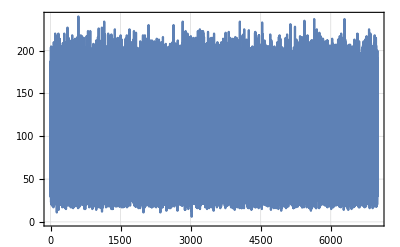
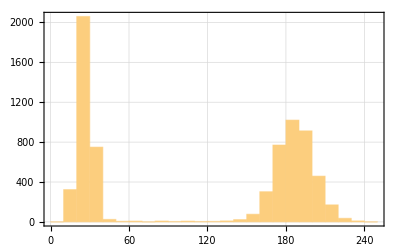

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
(*(*extract important parameters*)
timeRamseyUS=parameters["time_ramsey_delay_us"];
timeDisplaceUS=parameters["time_eggs_heating_us"];
timePulseshapeUS=parameters["time_pulse_shape_rolloff_us"]*parameters["enable_pulse_shaping"];
phaseRamseyTurns=First@parameters["phase_ramsey_anti_turns_list"];

(*calculate approximate displacement time*)
timeEGGSus=timeDisplaceUS+timePulseshapeUS*(2.*0.5);*)
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{6,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ns,1}];

(*take values and sort*)
datasetProcessed=Values[CollateData[datasetProcessed,{1}]];
datasetProcessed=SortBy[datasetProcessed,First];
```

### Fit

```mathematica
(*specify variables & parameters*)
ADJ=0.92;
ΩDJ=220*wkhz;
βDJ=1./(1.805*ms);
ηDJ=0.05;
numPhonons=20;
```

#### Create Fit Basis

```mathematica
(*data structures for fitting*)
βnArr=Array[Exp[-1/β0*√(#+1)]&,IntegerPart[numPhonons+1],0];
ΩnArr=(η0*Exp[-η0^2./2.])^Abs[Δn]*Array[LaguerreL[#,Abs[Δn],η0^2.]&,IntegerPart[numPhonons+1],0];
```

#### General Sine Fit

```mathematica
(*general sine fit*)
fitfunc=α*Sin[(1.*π)*(T)*(x-β)(*+ϕ*)]^2.+δ;
(*fitfunc=α*Sin[(1.*π)*(T)*(x-β)]^2.+δ;*)

(*set fixed values*)
fitfunc=fitfunc/.{
(*T->(timeRamseyUS+timeEGGSus)*1.*^-6,*)
(*β->Mean[dsN[[;;,1]]]*)
};
```

```mathematica
(*fit!*)
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
{
fitfunc
},
{
{α,0.7},
{β,Mean[dsN[[;;,1]]]},
{T,(timeRamseyUS+timeEGGSus)*1.*^-6},
{δ,Min[dsN[[;;,2]]]}
(*{ϕ,0.}*)
},
x
];
]
```

{0.001186,Null}

#### Get Fit Params

```mathematica
(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

### Plot

```mathematica
(*plot fitted data*)
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

```mathematica
(*plot summary figure*)
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black}
],
Show[
ListPlot[
{
dsN,
dsN
},
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (Hz)",{Black,Directive[15]}],
Style["Motional Ramsey (T_Delay = "<>ToString[timeRamseyUS]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]}},
Joined->{False,True}
],
fitPlot
]
};
```

### Show

0.

| Estimate | Standard Error | Confidence Interval
α | 0.554919 | 0.0429451 | {0.468054,0.641783}
β | 786399. | 13.108 | {786373.,786426.}
T | 0.000965247 | 0.0000235796 | {0.000917552,0.00101294}
δ | 0.0764682 | 0.027499 | {0.0208462,0.13209}

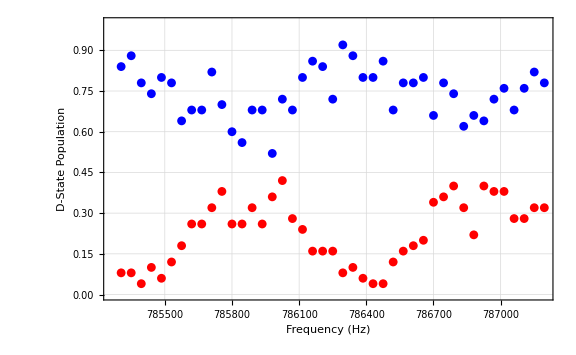
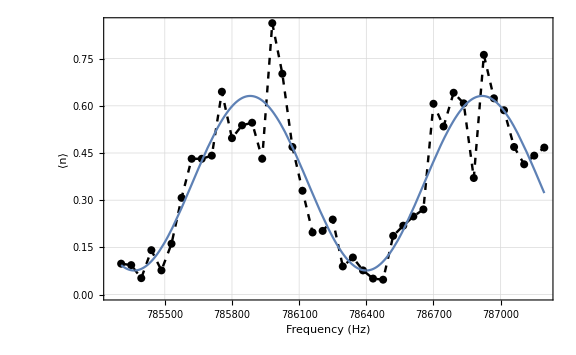

```mathematica
phaseRamseyTurns
fitParams
summaryFigure
```

## antisqueeze phase sweep

```mathematica
rid=85208;
```

### Import

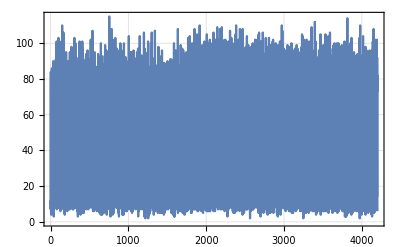
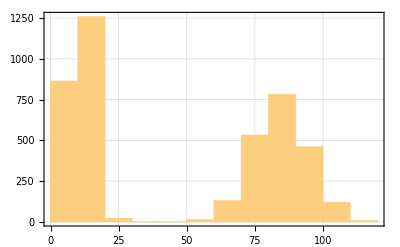

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,4,2}]],3];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*{ftwToFrequencyMHz,ftwToFrequencyMHz*1000.,1./(2.^16.-1.),1}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*phase unwrap*)
dsR[[;;,1]]=Mod[dsR[[;;,1]],1,-0.5];
dsB[[;;,1]]=Mod[dsB[[;;,1]],1,-0.5];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

Divide::indet: Indeterminate expression 0./0. encountered.

### Fit

```mathematica
fitfunc=α*Sin[(1.*π)*ϕ+γ]^2.+β;
```

```mathematica
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
fitfunc,
{
{α,0.8},
{γ,0.},
{β,0.}
},
ϕ
];
]
```

NonlinearModelFit::nrlnum: The function value {0.781568-1. Optimization`FindFit`y$1695711} is not a list of real numbers with dimensions {1} at {α,γ,β} = {0.8,0.,0.}.

NonlinearModelFit::nrlnum: The function value {0.781568-1. Optimization`FindFit`y$1695722} is not a list of real numbers with dimensions {1} at {α,γ,β} = {0.8,0.,0.}.

{0.0517003,Null}

```mathematica
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"],
{Background->White}
];
```

NonlinearModelFit::nrlnum: The function value {0.781568-1. Optimization`FindFit`y$1695731} is not a list of real numbers with dimensions {1} at {α,γ,β} = {0.8,0.,0.}.

NonlinearModelFit::nrlnum: The function value {0.781568-1. Optimization`FindFit`y$1695738} is not a list of real numbers with dimensions {1} at {α,γ,β} = {0.8,0.,0.}.

### Plot

```mathematica
fitPlot=
Plot[
fitRes[ϕ],
{ϕ,dsN[[1,1]],dsN[[-1,1]]}
];
```

Plot::plld: Endpoints for ϕ in {ϕ,0.451497,0.451497} must have distinct machine-precision numerical values.

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue,Black}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
],
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{Style["Antidisplace Phase (turns)",{Black,Directive[15]}],
Style["Antidisplace Phase Offset Sweep (T_Delay = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Black}
],
fitPlot
]
};
```

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

### Show

Indeterminate

Missing[KeyAbsent,att_squeeze_db]

NonlinearModelFit::nrlnum: The function value {0.781568-1. Optimization`FindFit`y$1695873} is not a list of real numbers with dimensions {1} at {α,γ,β} = {0.8,0.,0.}.

NonlinearModelFit[{{0.451497,InterpolatingFunction[…][Clip[{Indeterminate},{0.,0.8}]]}},β+α Sin[γ+3.14159 ϕ]^2.,{{α,0.8},{γ,0.},{β,0.}},ϕ][ParameterConfidenceIntervalTable]

Plot::plld: Endpoints for ϕ in {ϕ,0.451497,0.451497} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]].

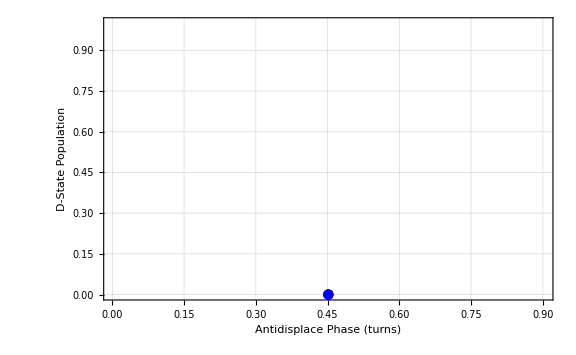
{-Graphics-,Show[-Graphics-,Plot[fitRes[ϕ],{ϕ,dsN⟦1,1⟧,dsN⟦-1,1⟧}]]}

```mathematica
Max[dsRatio[[;;,2]]]
parameters["att_squeeze_db"]
fitParams
summaryFigure
```

## squeeze time sweep

```mathematica
rid=52276;
```

### Import

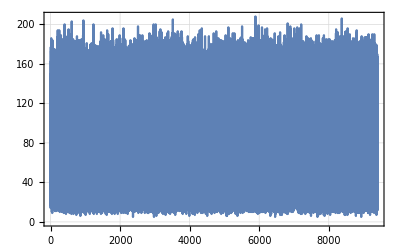
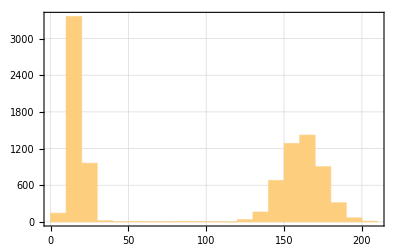
{-Graphics-,-Graphics-,{25.,{24.4565,50.,8.1087,11.1739,10.1522,23.4348,5.04348,4.02174,20.3696,44.8913,26.5,38.7609,47.9565,28.5435,41.8261,40.8043,43.8696,35.6957,32.6304,17.3043,25.4783,48.9783,46.9348,16.2826,34.6739,9.13043,7.08696,36.7174,37.7391,3.,31.6087,22.413,42.8478,18.3261,13.2174,30.587,14.2391,39.7826,19.3478,12.1957,45.913,27.5217,6.06522,21.3913,15.2609,29.5652,33.6522},{0.},{752.2},0}}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,5,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1./1000.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];

(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

InterpolatingFunction::dmval: Input value {0.827586} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.942308} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.859649} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

### Plot

```mathematica
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Probability",{Black,Directive[15]}],None},
{Style["Displace Time (μs)",{Black,Directive[15]}],
Style["Displace Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue}
],
ListPlot[
{
dsN
},
PlotRange->{Automatic,{0.,1.}},
(*PlotRange->{Automatic,Full},*)
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{Style["Displace Time (μs)",{Black,Directive[15]}],
Style["Displace Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Black}
]
};
```

### Show

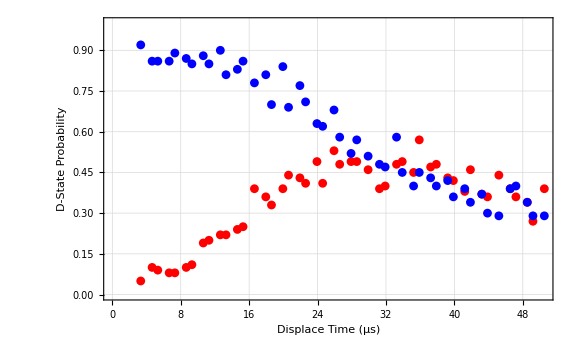
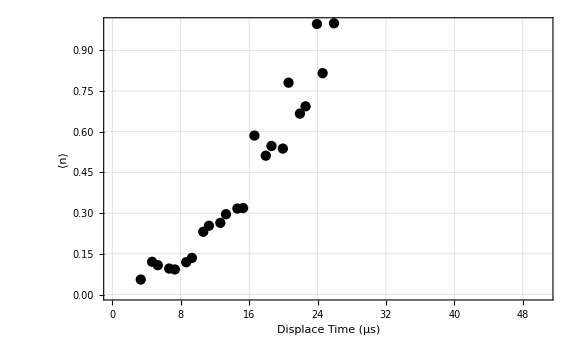

```mathematica
summaryFigure
```

## delay time sweep

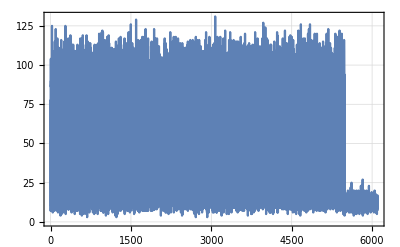
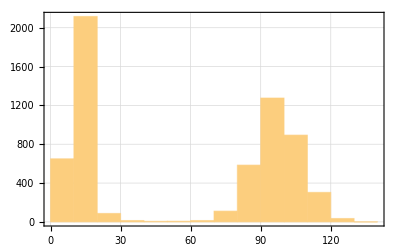

```mathematica
rid=41097;
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
};
```

```mathematica
dataset=dataset[[;;5700]];
```

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,6,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.*^-3,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];

(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
(*tmp remove*)
(*dsr[[;;,2]]=*)
(*tmp remove*)
```

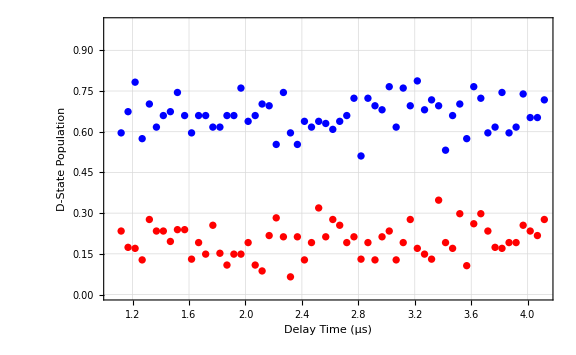

```mathematica
squeezeFreqSweep=ListPlot[
{dsR,dsB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Delay Time (μs)",{Black,Directive[15]}],Style["Delay Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Blue}
(*PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
]
```

## rabi flopping readout

## Import

```mathematica
rid=36295;

datafile=ImportDatasetARTIQ[directoryString,#]&[rid]
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"],
parameters["phase_antisqueeze_turns_list"],
parameters["freq_squeeze_khz_list"],
parameters["enable_antisqueezing"]
}
```

## Process

```mathematica
dataset=dataset[[;;,{1,5,7,2}]]
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.,1./1000.,1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{3,4}]];

dsR=ThresholdCounts[dsR,2];
dsR=Values[CollateData[dsR,{1}]];
dsR=SortBy[dsR,First];

dsB=ThresholdCounts[dsB,2];
dsB=Values[CollateData[dsB,{1}]];
dsB=SortBy[dsB,First];
```

## Plot

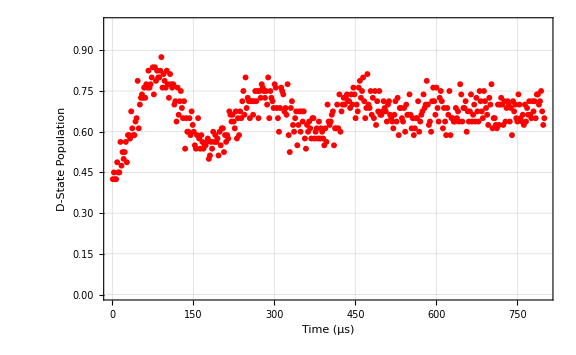

```mathematica
yzsg1=ListPlot[
{(*dsRA,dsRS,*)dsB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Time (μs)",{Black,Directive[15]}],Style["Squeeze Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Red,Black}(*,
PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},{Above,Right}],
PlotLegends->{"S^†(ξ) S(ξ)","S(ξ)"}*)
];
```

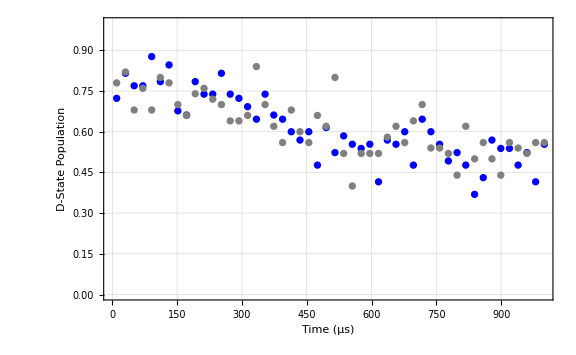

```mathematica
ListPlot[
{dsRB,dsBB},
PlotRange->{Automatic,{0,1}},
FrameLabel->{ 
{Style["D-State Population",{Black,Directive[15]}],None},
{Style["Time (μs)",{Black,Directive[15]}],Style["Squeeze Time Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
PlotStyle->{Blue,Gray}(*,
PlotLabels->Placed[{"S^†(ξ)S(ξ)","S(ξ)"},Above],
PlotLegends->{"S(ξ) S^†(ξ)","S(ξ)"}*)
]
```

## Show

```mathematica
Show[yzsg1]
```

## 2d sweep

```mathematica
rid=35715;
```

```mathematica
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}

dataset=dataset[[;;,{1,6,4,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.(*ftwToFrequencyMHz*),1/(2^15-1),1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{2,3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{2,3,4}]];
```

{11.,{50.}}

```mathematica
dsR=ThresholdCounts[dsR,-1];
dsR=CollateData[dsR,{2,1}];
dsR=Values[#][[;;,{1,3}]]&/@dsR;
(*dsR=SortBy[dsR,First];*)
```

```mathematica
dsB=ThresholdCounts[dsB,-1];
dsB=CollateData[dsB,{2,1}];
dsB=Values[#][[;;,{1,3}]]&/@dsB;
```

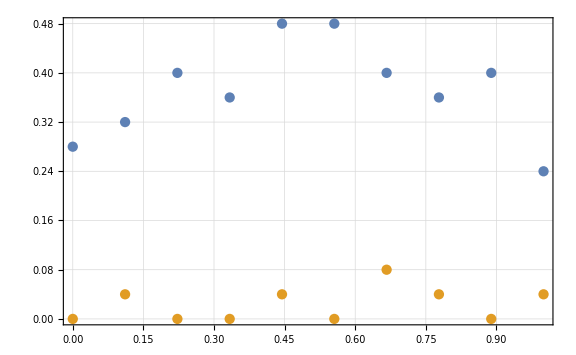

```mathematica
kk0=Values[Max[#[[;;,2]]]&/@dsR];
kk1=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

```mathematica
kk2=Values[Max[#[[;;,2]]]&/@dsR];
kk3=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

-Graphics-

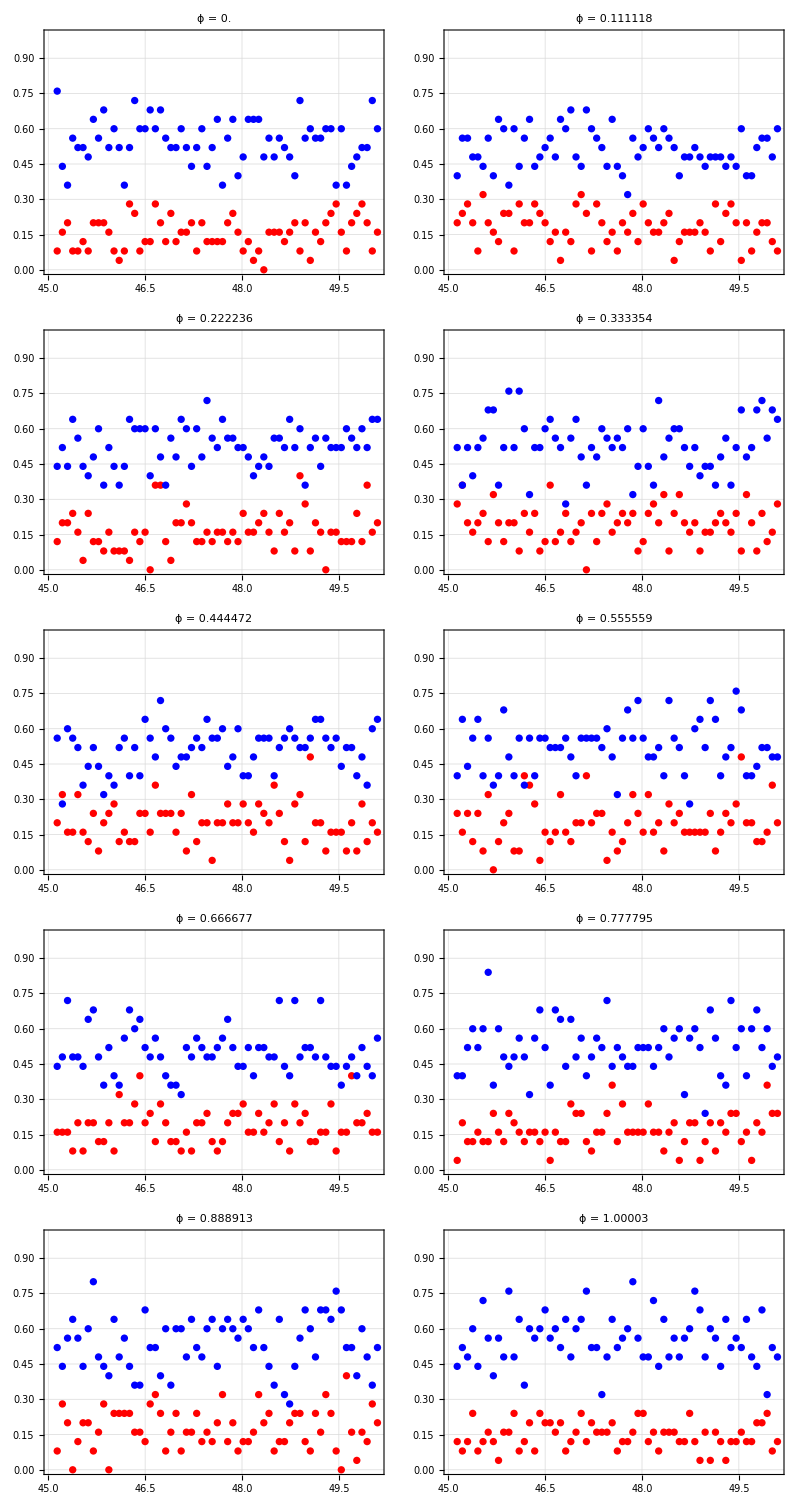

```mathematica
mzdp0=ListPlot[
{dsR[[#]],dsB[[#]]},
PlotRange->{Automatic,{0,1}},
PlotStyle->{Red,Blue},
PlotLabel->Style["ϕ = "<>ToString[Keys[dsR][[#]]],{FontSize->20}]
]&/@Range[Length[dsR]];

mzdp0=ArrayReshape[mzdp0,{5,2}];
Grid[mzdp0]
```

## sideband readout

## Import

```mathematica
rid=35715;
```

```mathematica
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}
```

## Process

```mathematica
dataset=dataset[[;;,{1,6,4,2}]];
dataset=Transpose[Transpose[dataset]*{ftwToFrequencyMHz,1./1000.(*ftwToFrequencyMHz*),1/(2^15-1),1}];
freqCenter=Mean[dataset[[;;,1]]];
dsR=Select[dataset,#[[1]]<freqCenter&][[;;,{2,3,4}]];
dsB=Select[dataset,#[[1]]>=freqCenter&][[;;,{2,3,4}]];
```

```mathematica
dsR=ThresholdCounts[dsR,-1];
dsR=CollateData[dsR,{2,1}];
dsR=Values[#][[;;,{1,3}]]&/@dsR;
(*dsR=SortBy[dsR,First];*)
```

```mathematica
dsB=ThresholdCounts[dsB,-1];
dsB=CollateData[dsB,{2,1}];
dsB=Values[#][[;;,{1,3}]]&/@dsB;
```

```mathematica
kk0=Values[Max[#[[;;,2]]]&/@dsR];
kk1=Values[Min[#[[;;,2]]]&/@dsR];
ListPlot[{Transpose[{Keys[dsR],kk0}],Transpose[{Keys[dsR],kk1}]}]
```

-Graphics-

## wsec sweep (w/PSK fit)

```mathematica
rid=49980;
```

### Import & Examine

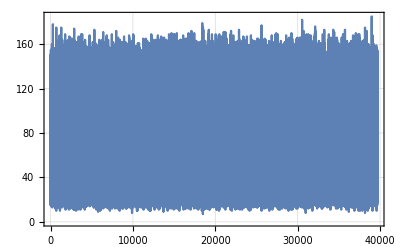
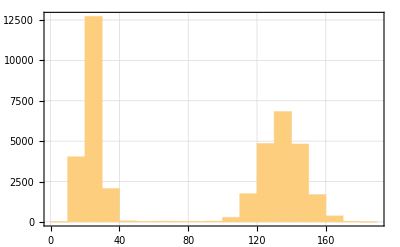

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
(*MatrixForm[{
parameters["att_squeeze_db"],
parameters["phase_antisqueeze_turns_list"],
parameters["enable_antisqueezing"]
}]*)
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,2,4}]],2];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.,1./khz}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{3,2}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{3,2}]];
(*collate data*)
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process ratio*)
dsN=Transpose[{dsR[[;;,1]]-Mean[dsR[[;;,1]]],CoherentC[dsR[[;;,2]]/dsB[[;;,2]]]}];
```

### Plot

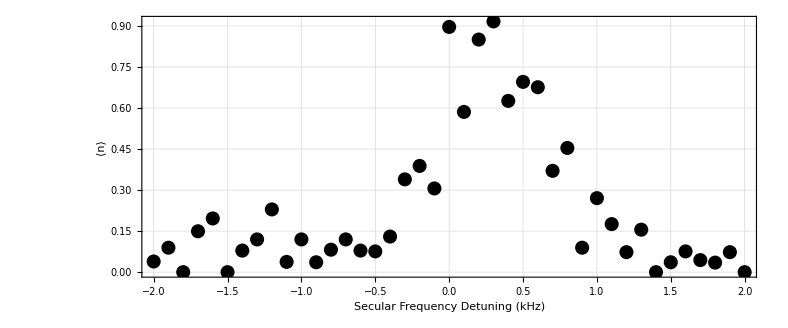

```mathematica
dataPlot=ListPlot[
{
dsN
},
PlotRange->{Automatic,Automatic},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Secular Frequency Detuning (kHz)",{Black,Directive[15]}],
Style["PSK(0)",{Black,Directive[15]}]
}
},
PlotStyle->{(*Red,Blue,*)Black},
AspectRatio->Full,
ImageSize->{788,328}
]
```

### fit

```mathematica
PSKFunc[psknum_]:=With[
{
phiArr=Riffle[ConstantArray[0.,#],ConstantArray[π,#]]&[IntegerPart[(psknum+1)/2]],
detArr=(δ*T)*Range[0,IntegerPart[#]]/(#+1.)&[psknum]
},
Return[
(Ω*T/(psknum+1.))*Sinc[δ*T/(2.*(psknum+1.))]*Exp[-(ⅈ*δ)*T/(2.*(psknum))]*Total[Exp[ⅈ*(detArr+phiArr)]]
];
];
```

```mathematica
th0=PSKFunc[5];
(*th1=th0/.{δ->-δ};
fitfunc=th0*th1//Expand//FullSimplify;
fitfunc=Abs[fitfunc/.{δ->δ*wkhz}];*)
fitfunc=(Ω*T)^2.*Sinc[(δ*T*wkhz)/2.]^2.;
(*fitfunc=Abs[th0/.{δ->(δ*wkhz)}]^2.;*)
fitfunc=Abs[th0/.{δ*T->(δ*T*wkhz+ϕ)}]^2.;
```

{0.008335,Null}

| Estimate | Standard Error | Confidence Interval
Ω | 13616.9 | 743.559 | {12111.6,15122.2}
T | 0.000333745 | 0.0000157504 | {0.00030186,0.00036563}
ϕ | 2.65687 | 0.113108 | {2.42789,2.88584}

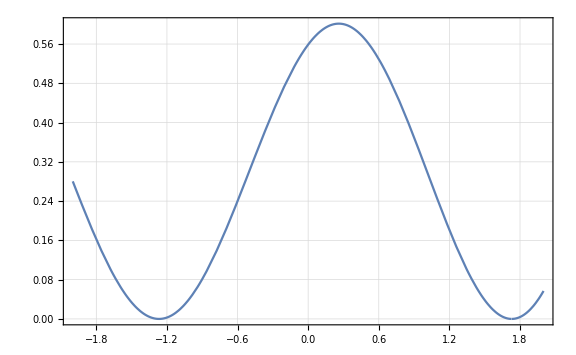

```mathematica
AbsoluteTiming[
fitRes=NonlinearModelFit[
dsN,
fitfunc,
{
{Ω,1.*wkhz},
{T,1.*ms},
{ϕ,0.}
},
δ
];
]
Style[
fitRes["ParameterConfidenceIntervalTable"],
{Background->White}
]
fitPlot=
Plot[
fitRes[δ],
{δ,dsN[[1,1]],dsN[[-1,1]]}
]
```

### show

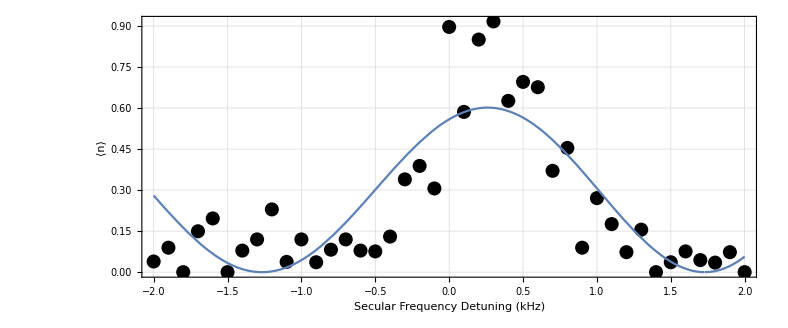

```mathematica
Show[
dataPlot,
fitPlot
]
```

## phase sweep

```mathematica
rid=50289;
```

## Import & Examine

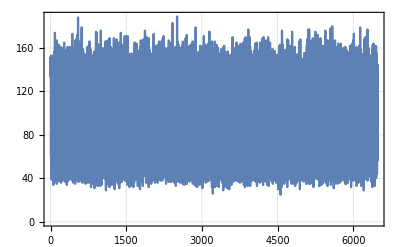
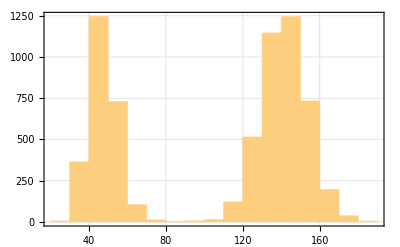

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]]
(*MatrixForm[{
parameters["att_squeeze_db"],
parameters["phase_antisqueeze_turns_list"],
parameters["enable_antisqueezing"]
}]*)
}&[dataset[[;;,2]]]
```

## Process

```mathematica
parameters["freq_eggs_heating_carrier_mhz_list"]
```

{30.}

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,2,4}]],2];
(*convert units*)
datasetProcessed=Transpose[
Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.,1./khz}
];
freqCenter=Mean[datasetProcessed[[;;,1]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{3,2}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{3,2}]];
(*collate data*)
dsR=Values[CollateData[dsR,{1}]//KeySort];
dsB=Values[CollateData[dsB,{1}]//KeySort];
```

```mathematica
(*process ratio*)
dsN=Transpose[
{
dsR[[;;,1]]+30.*^3(*Mean[dsR[[;;,1]]]*),
CoherentC[dsR[[;;,2]]/dsB[[;;,2]]]
}
];
```

## Plot 2

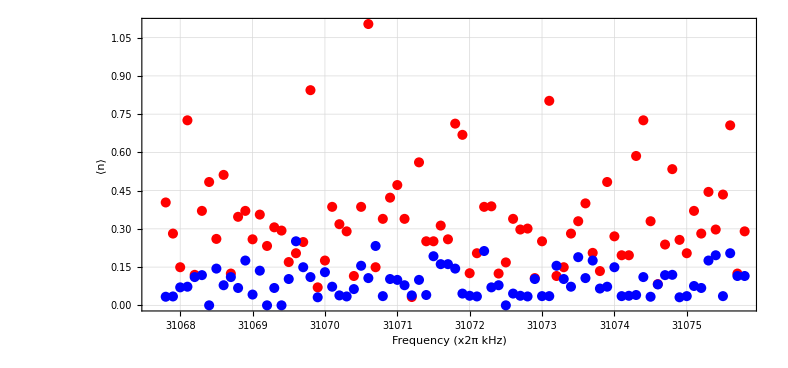

```mathematica
dataPlot=ListPlot[
{
dsNOff,
dsNOn
},
PlotRange->{Full,Full},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Frequency (x2π kHz)",{Black,Directive[15]}],
Style["Single-Tone Pulse Shaping",{Black,Directive[15]}]
}
},
PlotStyle->{
Red,
Blue
},
AspectRatio->Full,
(*FrameTicks->{
{Automatic,Automatic},
{xTicks,Automatic}
},*)
(*ImageSize->Large*)
ImageSize->{788,368}
]
```

## Plot

```mathematica
xTicks=Transpose[{#,π*#}]&[Range[0,2,1/2]];
```

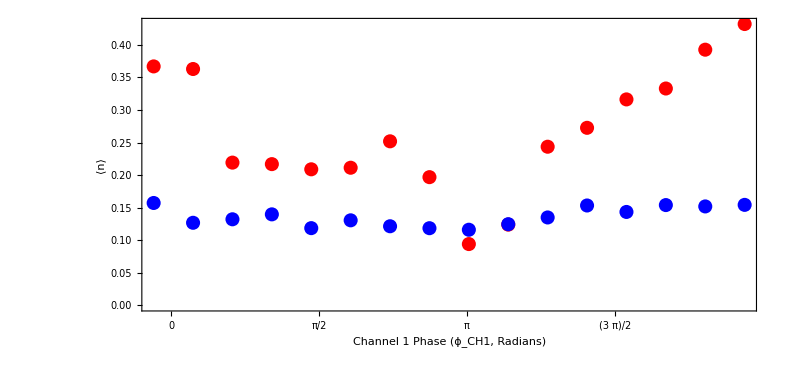

```mathematica
dataPlot=ListPlot[
{
dataShapeOFF,
dataShapeON
},
PlotRange->{Full,Full},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["Channel 1 Phase (ϕ_CH1, Radians)",{Black,Directive[15]}],
Style["Single-Tone Pulse Shaping",{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue},
AspectRatio->Full,
FrameTicks->{
{Automatic,Automatic},
{xTicks,Automatic}
},
(*ImageSize->Large*)
ImageSize->{788,368}
]
```

## tickle freq sweep

```mathematica
rid=54812;
```

## Process

### Import

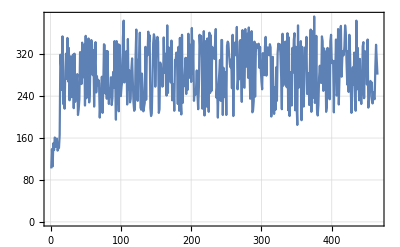
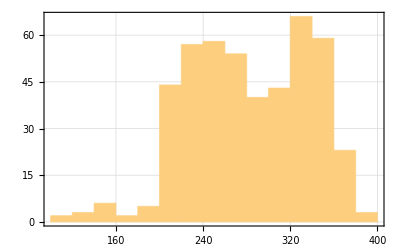
{-Graphics-,-Graphics-,(25.)}

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_tickle_db"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*datasetProcessed=ThresholdCounts[dataset[[;;,{1,2}]],2];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*freqCenter=1000;*)*)
```

```mathematica
(*process dataset*)
datasetProcessed=Transpose[
Transpose[dataset[[;;,{1,2}]]]
*{ftwToFrequencyMHz*(1.*^3),1}
];
datasetProcessed=Values[CollateData[datasetProcessed,{1}]];
```

### Plot

```mathematica
summaryFigure=ListPlot[
{
datasetProcessed
},
PlotRange->{Automatic,Full},
FrameLabel->{ 
{Style["Counts (arb.)",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Tickle Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
];
```

## Show

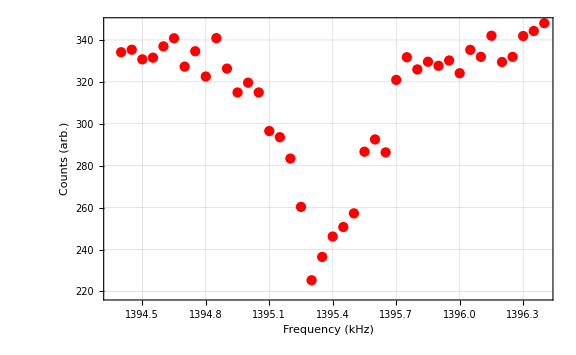

```mathematica
summaryFigure
```

```mathematica
102.2919-1.395/2
```

101.594

## tickle freq sweep (timestamped)

```mathematica
rid=54661;
```

## Process

### custom import func bc i’m lazy

```mathematica
(*import dataset from dir and filename, return dataset and parameters*)
ImportDatasetARTIQTimestamped[filedirs_:(_String|_List),ridName:(_String|_Integer)]:=Module[
{
filenameDJ,
fileDirectories=filedirs,

(*dataset values*)
datasetRaw,
timestampedCounts,
parameterList
},

(*ensure filedirs is a list*)
If[Head[fileDirectories]==String,
fileDirectories={filedirs}
];

(*ensure import directory exists*)
If[!AnyTrue[DirectoryQ/@filedirs],

(*stop execution if import directory doesn't exist*)
MessageDialog["Failure :(\nError: Import directory not found."];
FrontEndTokenExecute["EvaluatorAbort"];
];


filenameDJ=FileNames["*"<>ToString[#]<>"*.h5",filedirs,Infinity]&[ridName];

(*stop execution if file doesn't exist*)
If[Length[filenameDJ]==0,

MessageDialog["Failure :(\nError: Specified file not found ("<>ToString[ridName]<>")."];
FrontEndTokenExecute["EvaluatorAbort"],

filenameDJ=First@filenameDJ;
];

(*extract file results as list and parameters as an association*)
datasetRaw=Import[filenameDJ,{"/datasets/results"}];
timestampedCounts=Import[filenameDJ,{"/datasets/timestamped_counts"}];
parameterList=Import[filenameDJ,{"Attributes","/arguments"}];

Return[{datasetRaw,timestampedCounts,parameterList}];
];
```

### Import

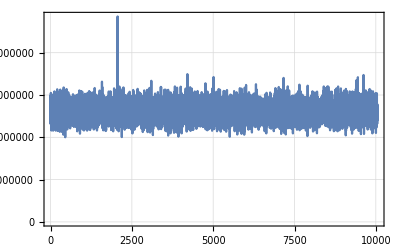
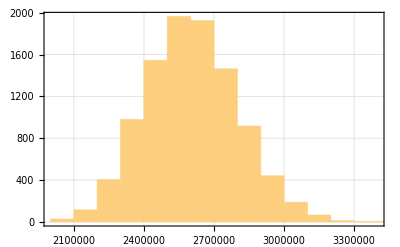
{-Graphics-,-Graphics-,(19.)}

```mathematica
datafile=ImportDatasetARTIQTimestamped[directoryString,ToString[#]]&[rid];
{dataset,timestampedCounts,parameters}=datafile;
{
ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],
Histogram[#,ImageSize->Scaled[0.3]],
MatrixForm[{
parameters["att_tickle_db"]
}]
}&[dataset[[;;,2]]]
```

### Process

```mathematica
(*convert units*)
timestampedCountsus=timestampedCounts*(1.*^-3)*UnitStep[timestampedCounts];
datasetConverted=Transpose[
Transpose[dataset[[;;,{1,2,3,4}]]]
*{ftwToFrequencyMHz*(1.*^3),1.*^-3,asfToAmplitudePCT,1.*^-3}
];
```

```mathematica
(*select axes config we want*)
datasetProcessed=Join[datasetConverted[[;;,{1}]],timestampedCountsus,2];
```

```mathematica
(*datasetProcessed=Values[CollateData[datasetProcessed,{1}]];*)
```

```mathematica
th0=GroupBy[datasetProcessed,First]//KeySort;
```

```mathematica
th0//Keys
```

{1256.7,1248.7,1244.1,1249.3,1250.5,1255.3,1248.8,1250.1,1258.1,1260.2,1260.8,1251.6,1252.4,1254.7,1254.4,1251.4,1247.7,1260.7,1253.3,1256.3,1248.9,1256.1,1244.5,1257.8,1258.8,1255.7,1259.,1252.,1255.9,1243.3,1261.,1250.,1257.7,1247.,1261.8,1251.1,1258.3,1246.4,1253.4,1245.,1243.6,1253.8,1262.5,1246.9,1250.9,1244.7,1257.1,1259.5,1258.2,1262.2,1245.3,1258.5,1260.,1254.3,1256.4,1248.3,1252.9,1262.3,1260.5,1255.6,1249.6,1258.6,1250.7,1255.1,1252.8,1249.5,1243.4,1253.6,1245.5,1259.6,1243.,1260.3,1254.5,1244.8,1246.6,1260.1,1253.2,1245.9,1244.3,1243.1,1260.6,1256.5,1247.3,1254.,1255.5,1262.6,1252.5,1250.2,1259.9,1243.9,1261.9,1242.7,1259.2,1245.7,1247.4,1246.2,1259.7,1252.2,1262.1,1254.9,1243.8,1243.2,1242.8,1247.8,1248.5,1260.9,1242.6,1247.6,1244.4,1256.9,1249.4,1259.4,1256.2,1257.,1245.4,1258.7,1253.7,1261.4,1248.1,1244.2,1242.9,1248.4,1254.2,1254.8,1250.3,1261.5,1255.8,1244.,1254.6,1245.2,1257.2,1256.8,1256.,1252.3,1248.6,1251.7,1262.4,1249.1,1254.1,1243.5,1261.7,1251.2,1253.1,1258.9,1247.2,1257.3,1249.9,1244.6,1250.4,1262.,1260.4,1253.5,1252.7,1261.6,1259.3,1249.8,1246.3,1247.1,1252.1,1259.8,1259.1,1247.5,1246.1,1257.9,1261.3,1251.3,1243.7,1251.9,1257.6,1245.8,1244.9,1258.4,1255.4,1261.2,1245.1,1249.7,1250.6,1249.,1257.5,1257.4,1253.9,1252.6,1253.,1246.7,1251.5,1261.1,1247.9,1246.8,1256.6,1255.,1246.,1245.6,1258.,1250.8,1246.5,1249.2,1248.2,1255.2,1251.,1251.8,1248.}

```mathematica
timestampedCounts//Dimensions
```

{10050,200}

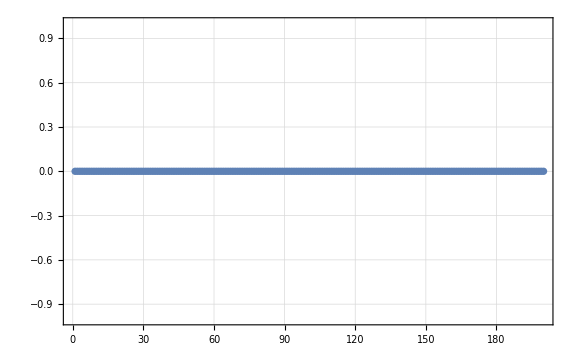

```mathematica
ListPlot[datasetProcessed[[#,2;;]]]&[1011]
```

### Plot

```mathematica
summaryFigure=ListPlot[
{
datasetProcessed
},
PlotRange->{Automatic,Full},
FrameLabel->{ 
{Style["Counts (arb.)",{Black,Directive[15]}],None},
{Style["Frequency (kHz)",{Black,Directive[15]}],
Style["Tickle Sweep\nRID: "<>ToString[rid],{Black,Directive[15]}]}
},
Joined->{False,True,False,True},
PlotStyle->{
{Red},
{Red,Dashed},
{Blue},
{Blue,Dashed}
}
];
```

## Show

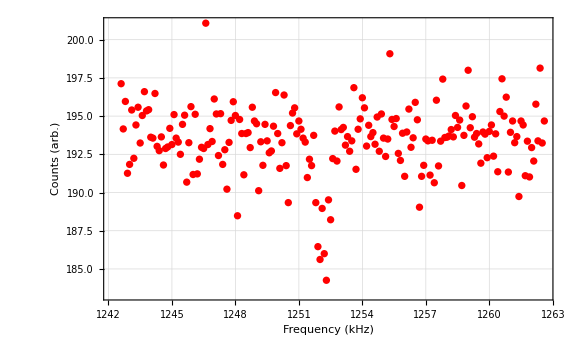

```mathematica
summaryFigure
```

## Show

```mathematica
(*timestampedCountsus=timestampedCounts*1.*^-6;
datasetTimestamped=dataset;*)
```

```mathematica
datasetConverted=datasetTimestamped
```

```mathematica
{ftwToFrequencyMHz,1.*^-6,1,1}*#&/@datasetTimestamped[[;;5,;;4]]
```

{{5.39577×10^6,3.35541×10^6,57.,999999.},{5.3511×10^6,3.03556×10^6,57.,999999.},{5.35926×10^6,3.06692×10^6,57.,999999.},{5.41123×10^6,3.06898×10^6,57.,999999.},{5.35067×10^6,3.16277×10^6,57.,999999.}}

```mathematica
resFull[[;;3,;;4]]//MatrixForm
```

(5.39577×10^6 | 3.35541×10^6 | 57. | 999999.
5.3511×10^6 | 3.03556×10^6 | 57. | 999999.
5.35926×10^6 | 3.06692×10^6 | 57. | 999999.)

```mathematica
resFull//Dimensions
```

{10050,204}

```mathematica
resFull[[1,;;6]]
```

{5.39577×10^6,3.35541×10^6,57.,999999.,7582,81977}

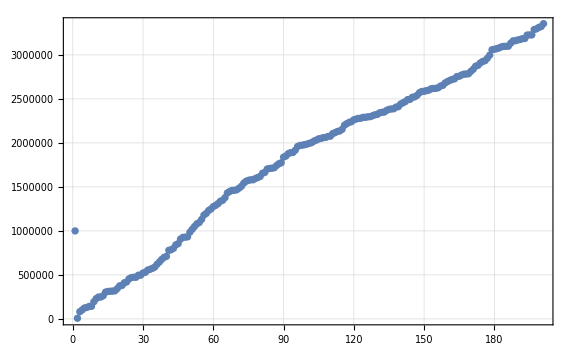

```mathematica
ListPlot[resFull[[1,4;;]]]
```

## laser scan (long term)

```mathematica
rid=72554;
```

```mathematica
discriminationFreqs={101.3};
```

## Import

```mathematica
datafile=ImportDatasetARTIQ[directoryString,#]&[rid];
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}
```

{Missing[KeyAbsent,att_squeeze_db],Missing[KeyAbsent,time_squeeze_us_list]}

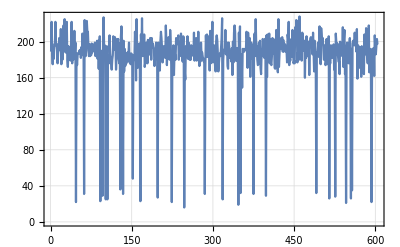
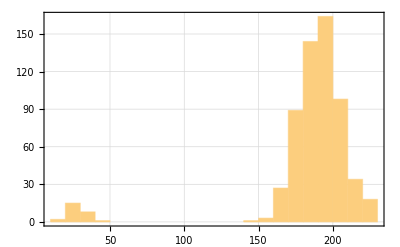

```mathematica
(*show histogram and time trace*)
{
ListLinePlot[
#[[;;]],
PlotRange->Full,
ImageSize->Scaled[0.3]
],
Histogram[
#,
ImageSize->Scaled[0.3]
]
}&[dataset[[;;;;10,2]]]
```

## Process

### Base Processing

```mathematica
(*select relevant indices*)
datasetProcessed=dataset[[;;,{1,2}]];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{ftwToFrequencyMHz,1}
];
```

```mathematica
(*threshold counts and group by frequency*)
datasetProcessed=ThresholdCounts[datasetProcessed,2,"Threshold"->45];
(*convert d-state probability to s-state probability*)
datasetProcessed[[;;,2]]=1.-datasetProcessed[[;;,2]];
```

```mathematica
(*group data*)
datasetProcessed=GroupBy[
datasetProcessed,
First(*->Last*)
]//KeySort;
```

### Plot Full Averaged

```mathematica
(*plot full averaged data*)
fullData=Values[Mean/@datasetProcessed];
```

```mathematica
(*prepare discrimination values*)
discriminationCriteria=Sort[discriminationFreqs];
```

```mathematica
{
(*plot in full*)
ListLinePlot[
fullData,
PlotRange->Full,
ImageSize->Scaled[0.31]
],

(*plot sidebands*)
ListLinePlot[
Select[fullData,#[[1]]<101.6&],
PlotRange->Full,
ImageSize->Scaled[0.31]
],

(*plot carrier*)
ListLinePlot[
Select[fullData,(#[[1]]>102.231)&&(#[[1]]<102.244)&],
PlotRange->Full,
ImageSize->Scaled[0.31]
]
}
```

### Extra

```mathematica
(*(*select only sideband data*)
th0=KeySelect[datasetProcessed,(#>101.5485)&&(#<101.5496)&];
th1=MovingAverage[#,50]&/@th0;
ListPlot[Values[Mean/@th0],PlotRange->Full]*)
```

```mathematica
(*yz0=#[[;;,2]]&/@th1;
yz0=(Transpose[{Range[Length[#]],#}]&/@yz0)//Values;
ListLinePlot[yz0,PlotRange->Full]*)
```

```mathematica
(*yz0[[;;,;;,2]]//Dimensions
f/@Transpose[yz0[[;;3,;;,2]]]*)
```

```mathematica
(*Mean/@Transpose[yz0[[;;,;;,2]]];
ListPlot[%]*)
```

### Specific Processing

#### Processing Func

```mathematica
(*processing function*)
processfunc[dataset_,numFilter_Integer:20]:=Module[
{
datasetFinal,

(*dataset length*)
dataLength=2500,

(*mean point pairs if we have 5000 points*)
datasetY=If[
Length[dataset]==2500,
dataset[[;;,2]],
Mean/@ArrayReshape[dataset[[;;,2]],{IntegerPart[Length[dataset[[;;,2]]]/2],2}]
]
},

(*apply mean filter*)
datasetY=MeanFilter[datasetY,numFilter];

(*make 3d w/y-axis as "time"*)
datasetFinal=Transpose[{
ConstantArray[dataset[[1,1]],2500],
Range[dataLength],
datasetY
}];

(*return*)
Return[datasetFinal[[;;;;5]]];
];
```

#### Actual

```mathematica
datasetProcessed//Head
```

Association

```mathematica
datasetProcessed[[1]]
```

{{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.},{101.259,1.}}

```mathematica
datasetProcessed//Keys
```

{101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.26,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.261,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.262,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.263,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.264,101.265,101.265,101.265,101.265,101.265,101.265,101.265,101.265,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.799,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.8,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.801,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.802,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.803,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.804,101.805,101.805,101.805,101.805,101.805,101.805,101.805,101.805,101.805,101.805,101.805}

```mathematica
datasetFinal=(processfunc/@datasetProcessed)//KeySort;
%//Dimensions
```

Transpose::nmtx: The first two levels of {{101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,101.259,«2490»},{1,2,3,4,5,6,7,8,9,10,«2490»},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

{302}

```mathematica
datasetFinalHCl35=KeySelect[datasetFinal,(#>101.545)&&(#<101.553)&]//Values;
datasetFinalHCl35=Flatten[datasetFinalHCl35,1];
%//Dimensions
```

{0}

```mathematica
datasetFinalH2Cl35=KeySelect[datasetFinal,(#>101.56)&&(#<101.58)&]//Values;
datasetFinalH2Cl35=Flatten[datasetFinalH2Cl35,1];
%//Dimensions
```

{0}

```mathematica
datasetFinalCarrier=KeySelect[datasetFinal,(#>102.234)&&(#<102.242)&]//Values;
datasetFinalCarrier=Flatten[datasetFinalCarrier,1];
%//Dimensions
```

{0}

### Plot

```mathematica
plotHCl35=ListDensityPlot[
datasetFinalHCl35,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];
```

```mathematica
plotH2Cl35=ListDensityPlot[
datasetFinalH2Cl35,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];
```

```mathematica
plotCarrier=ListDensityPlot[
datasetFinalCarrier,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];
```

## Show

```mathematica
{plotHCl35,plotH2Cl35,plotCarrier}
```

{-Graphics-,-Graphics-,-Graphics-}

## laser scan (long term) - RDX

```mathematica
rid=73350;
```

```mathematica
binSize=20;
discriminationFreqs={101.3};
```

## Import

```mathematica
(*import dataset*)
AbsoluteTiming[datafile=ImportDatasetARTIQ[directoryString,#]&[rid];]
{dataset,parameters}=datafile;
{
parameters["att_squeeze_db"],
parameters["time_squeeze_us_list"]
}
```

{1.22707,Null}

{Missing[KeyAbsent,att_squeeze_db],Missing[KeyAbsent,time_squeeze_us_list]}

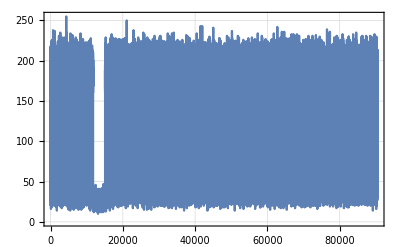
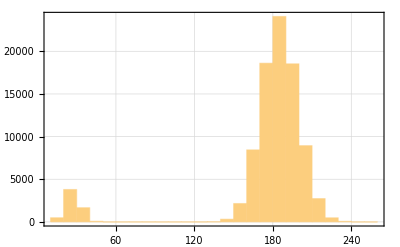

```mathematica
(*show histogram and time trace*)
{
ListLinePlot[
#[[;;]],
PlotRange->Full,
ImageSize->Scaled[0.3]
],
Histogram[
#,
ImageSize->Scaled[0.3]
]
}&[dataset[[;;;;10,2]]]
```

```mathematica
(*remove zeros - note: don't use this since it creates problems*)
(*dataset0=dataset[[;;113400]];
dataset1=dataset[[13560;;]];
dataset=Join[dataset0,dataset1];*)
```

```mathematica
(*get important parameters*)
timeReadoutUS=parameters["time_qubit_us"];
timeRunSeconds=Length[dataset]*(6.1+timeReadoutUS/(1.*^3))*1.*^-3;
```

## Process

### Base Processing

```mathematica
(*select relevant indices*)
datasetProcessed=dataset[[;;,{1,2}]];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{ftwToFrequencyMHz,1}
];
```

```mathematica
(*threshold counts and group by frequency*)
datasetProcessed=ThresholdCounts[datasetProcessed,2,"Threshold"->45];
(*convert d-state probability to s-state probability*)
datasetProcessed[[;;,2]]=1.-datasetProcessed[[;;,2]];
```

```mathematica
(*group data*)
datasetProcessed=GroupBy[
datasetProcessed,
First(*->Last*)
]//KeySort;
```

### Group Data Into Bins

```mathematica
(*select data*)
dataDJ=KeySelect[
datasetProcessed,
(#>101.5)(*&&(#<101.553)*)&
]//Values;
```

```mathematica
(*(*tmp remove - needed since not all arrays have same shape*)
dataDJ=dataDJ[[;;-2]];*)
```

```mathematica
(*rearrange correctly*)
dataDJ=Transpose[dataDJ,1<->2];
(*split data into bins, then transpose axes again*)
dataDJ=Partition[dataDJ,UpTo[binSize]];
dataDJ=Transpose[dataDJ,2<->3];
```

```mathematica
(*average data within each bin*)
dataDJ=Map[Mean,dataDJ,{2}];
```

### Fit Sinc

#### Fit Sinc Function

```mathematica
(*sinc - fit model*)
fitModel=1.-α^2./((x-β)^2.+α^2.)*(Sin[1.*π*γ √((x-β)^2.+α^2.)]^2.)-δ;
```

```mathematica
(*fit each data bin with a sinc function & extract freq*)
fitSinc[data_,timeUS_]:=Module[
{
(*fitting variables*)
fitModelDJ,
fitRes,
fitParams,

(*fit results/plots*)
rawDataPlot,
fittedDataPlot,
summaryResult,

(*guess parameters*)
guessα,
guessβ=data[[First@Ordering[data[[;;,2]],1],1]],
guessδ=1.-data[[First@Ordering[data[[;;,2]],-1],2]]
},

(*prepare fitting*)
fitModelDJ=fitModel/.{γ->timeUS};
guessα=2.*ArcSin[Sqrt[#]/(π*timeUS)]&[(1.-Min[data[[;;,2]]])-guessδ];

(*fit!*)
fitRes=NonlinearModelFit[
data,
{
fitModelDJ,
δ>0.
},
Transpose[{
{α,β,δ},
{guessα,guessβ,guessδ}
}],
x
];

(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];

(*plot data*)
rawDataPlot=ListLinePlot[
data,
PlotRange->Full
];
fittedDataPlot=Plot[
fitRes[x],
{x,data[[1,1]],data[[-1,1]]},
PlotRange->Full,
PlotStyle->Red
];
summaryResult={
fitParams,
Show[
rawDataPlot,
fittedDataPlot
]
};

Return[{β/.fitRes["BestFitParameters"],fitRes,summaryResult}]
];
```

#### Fit Sinc!

```mathematica
(*fit!*)
fittedSincData=ParallelMap[
fitSinc[#,timeReadoutUS]&,
dataDJ
];
```

#### Process Results

```mathematica
(*create x-axes (time) in minutes*)
fittedDataTimeMinutes=Range[#]*(timeRunSeconds/60.*1/#)&[Length[fittedSincData]];
```

```mathematica
(*get abs data in MHz*)
fittedSincAbsFreqData=2.*fittedSincData[[;;,1]];
fittedSincAbsFreqData=Transpose[{fittedDataTimeMinutes,fittedSincAbsFreqData}];
```

```mathematica
(*convert absolute data in MHz to absolute relative drift in kHz*)
fittedSincAbsFreqDataDriftkHz=fittedSincAbsFreqData;
fittedSincAbsFreqDataDriftkHz[[;;,2]]-=Mean[fittedSincAbsFreqData[[;;,2]]];
fittedSincAbsFreqDataDriftkHz[[;;,2]]*=(1.*^3);
```

```mathematica
(*get results in relative drift in abs kHz with errors*)
fittedSincAbsFreqDataDriftkHzErr=#[[2]]["ParameterConfidenceIntervalTableEntries"][[2,1;;2]]&/@fittedSincData;
fittedSincAbsFreqDataDriftkHzErr=Around@@@fittedSincAbsFreqDataDriftkHzErr;
fittedSincAbsFreqDataDriftkHzErr=Transpose[{fittedDataTimeMinutes,2.*(1.*^3)*fittedSincAbsFreqDataDriftkHzErr}];
fittedSincAbsFreqDataDriftkHzErr[[;;,2]]-=fittedSincAbsFreqDataDriftkHzErr[[;;,2]];
```

### Plot!

#### Plot Fitted Sinc Summary

```mathematica
(*plot fitted results*)
fittedSincSummaryPlot=ListPlot[
{
fittedSincAbsFreqDataDriftkHz,
fittedSincAbsFreqDataDriftkHz
},
FrameLabel->{ 
{Style["Frequency - Abs. (kHz)",{Black,Directive[15]}],None},
{
Style["Time (mins)",{Black,Directive[15]}],
Style["Carrier Frequency Drift (Laser Scan)",{Black,Directive[15]}]
}
},
(*PlotRange->Full,*)
Joined->{False,True},
PlotStyle->{{Red,Thickness[0.004]},{Red,Dashed,Thickness[0.002],Opacity[0.3]}}
];
```

#### Fit Line to Extract Drift From Fitted Sinc Summary

```mathematica
(*filter noisy data to ease fitting*)
filteredDataTMP=fittedSincAbsFreqDataDriftkHz;
filteredDataTMP[[;;,2]]=MedianFilter[filteredDataTMP[[;;,2]],8];

(*try to fit drift results & plot results*)
fittedSincSummaryFitWeights=1./(#["Error"])^2.&/@fittedSincAbsFreqDataDriftkHzErr[[;;,2]];
(*fit!*)
fittedSincSummaryFitRes=LinearModelFit[
filteredDataTMP,
{1,t},
t
(*Weights->fittedSincSummaryFitWeights*)
];
```

```mathematica
(*plot summary*)
fittedSincSummaryFitPlot=Plot[
fittedSincSummaryFitRes[t],
{t,fittedDataTimeMinutes[[1]],fittedDataTimeMinutes[[-1]]}
];
```

```mathematica
(*create parameter table*)
fittedSincSummaryFitParams=Style[
fittedSincSummaryFitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];
```

#### Create List Density Plot

```mathematica
(*format data for list density plot*)
timeTraceData=Table[
{##[[1]],i,##[[2]]}&@dataDJ[[i,j]],
{i,Range[Dimensions[dataDJ][[1]]]},
{j,Range[Dimensions[dataDJ][[2]]]}
];
timeTraceData=Flatten[timeTraceData,1];
```

```mathematica
timeTracePlot=ListDensityPlot[
timeTraceData
];
```

#### Plot Full Averaged

```mathematica
(*plot full averaged data*)
fullData=Values[Mean/@datasetProcessed];
```

```mathematica
(*prepare discrimination values*)
discriminationCriteria=Sort[discriminationFreqs];
```

```mathematica
fullDataAveragedPlots={
(*plot in full*)
ListLinePlot[
fullData,
PlotRange->Full,
ImageSize->Scaled[0.31]
],

(*plot sidebands*)
ListLinePlot[
Select[fullData,#[[1]]<=101.6&],
PlotRange->Full,
ImageSize->Scaled[0.31]
],

(*plot carrier*)
ListLinePlot[
Select[fullData,(#[[1]]>101.6)&&(#[[1]]<102.244)&],
PlotRange->Full,
ImageSize->Scaled[0.31]
]
};
```

## Show

| Estimate | Standard Error | Confidence Interval
1 | 0.759601 | 0.0110358 | {0.737853,0.781348}
t | -0.00672444 | 0.000113851 | {-0.0069488,-0.00650008}

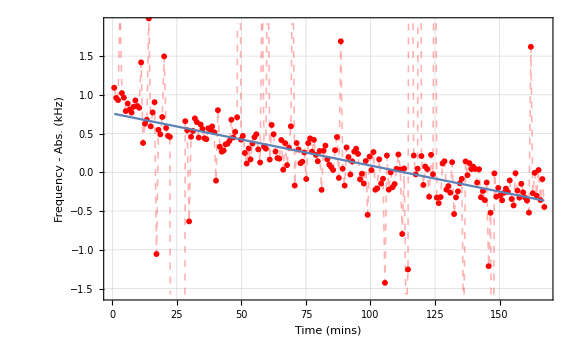

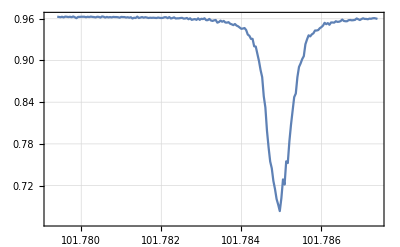
{-Graphics-,-Graphics-,-Graphics-}

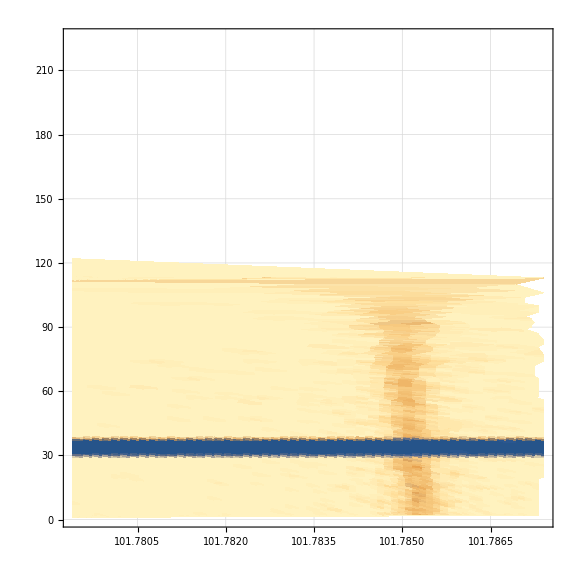

```mathematica
fittedSincSummaryFitParams
Show[fittedSincSummaryPlot,fittedSincSummaryFitPlot]
fullDataAveragedPlots
timeTracePlot
```

#### old idk

```mathematica
(*plotHCl35=ListDensityPlot[
datasetFinalHCl35,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];*)
```

```mathematica
(*plotH2Cl35=ListDensityPlot[
datasetFinalH2Cl35,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];*)
```

```mathematica
(*plotCarrier=ListDensityPlot[
datasetFinalCarrier,
PlotLegends->Automatic,
PlotRange->Full,
(*ColorFunction->,*)
ColorFunctionScaling->True,
FrameLabel->{ 
{Style["Repetition Number (#)",{Black,Directive[15]}],None},
{Style["Readout Frequency (AOM, MHz)",{Black,Directive[15]}],
Style["Laser Scan - RID: "<>ToString[rid],{Black,Directive[15]}]}
},
ImageSize->Scaled[0.38],
Mesh->None
];*)
```

## laser scan - sinc fit

```mathematica
rid=89689;
```

## Import

{1.37683,Null}

(4.35795×10^8 | 73.
4.35797×10^8 | 74.
4.35793×10^8 | 59.)

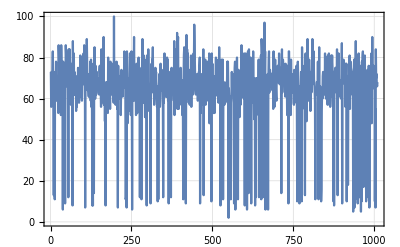
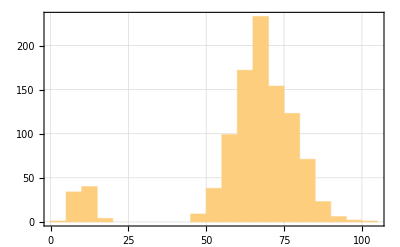

```mathematica
(*import dataset*)
AbsoluteTiming[datafile=ImportDatasetARTIQ[directoryString,#]&[rid];]
{dataset,parameters}=datafile;
dataset[[;;3]]//MatrixForm
(*show histogram and time trace*)
{
ListLinePlot[
#[[;;]],
PlotRange->Full,
ImageSize->Scaled[0.3]
],
Histogram[
#,
ImageSize->Scaled[0.3]
]
}&[dataset[[;;;;10,2]]]
```

```mathematica
(*get important parameters*)
timeReadoutUS=parameters["time_qubit_us"];
timeTriggerHoldoff=parameters["linetrigger.time_holdoff_ms"];
```

## Process

### Base Processing

```mathematica
(*select relevant indices*)
datasetProcessed=dataset[[;;,{1,2}]];
datasetProcessed=Transpose[
Transpose[datasetProcessed]*
{ftwToFrequencyMHz,1}
];
```

```mathematica
(*threshold counts and group by frequency*)
datasetProcessed=ThresholdCounts[datasetProcessed,2,"Threshold"->45];
(*convert d-state probability to s-state probability*)
datasetProcessed[[;;,2]]=1.-datasetProcessed[[;;,2]];
(*collate data*)
datasetProcessed=CollateData[datasetProcessed,{1}]//Values;
```

### Fit Sinc

#### Fit Sinc Function

```mathematica
(*sinc - fit model*)
fitModel=1.-α^2./((x-β)^2.+α^2.)*(Sin[1.*π*γ √((x-β)^2.+α^2.)]^2.)-δ;
```

```mathematica
(*fit each data bin with a sinc function & extract freq*)
fitSinc[data_,timeUS_:timeReadoutUS]:=Module[
{
(*fitting variables*)
fitModelDJ,
fitRes,
fitParams,

(*fit results/plots*)
rawDataPlot,
fittedDataPlot,
summaryResult,

(*guess parameters*)
guessα,
guessβ=data[[First@Ordering[data[[;;,2]],1],1]],
guessδ=1.-data[[First@Ordering[data[[;;,2]],-1],2]]
},

(*prepare fitting*)
(*fitModelDJ=fitModel/.{γ->timeUS};*)
fitModelDJ=fitModel/.{δ->0.};
guessα=2.*ArcSin[Sqrt[#]/(π*timeUS)]&[(1.-Min[data[[;;,2]]])-guessδ];

(*fit!*)
fitRes=NonlinearModelFit[
data,
{
fitModelDJ
(*δ>0.*)
},
Transpose[{
{α,β,γ},
{guessα,guessβ,timeUS}
}],
x
];

(*get fit params*)
fitParams=Style[
fitRes["ParameterConfidenceIntervalTable"][[1]],
{Background->White,FontColor->Black,FontSize->15}
];

(*plot data*)
rawDataPlot=ListLinePlot[
data,
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["P_(S - 1/2)",{Black,Directive[15]}],None},
{
Style["Frequency (MHz)",{Black,Directive[15]}],
Style["Laser Scan (T_Pulse = "<>ToString[timeReadoutUS]<>" μs, T_Holdoff = "<>ToString[timeTriggerHoldoff]<>" ms\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
];
fittedDataPlot=Plot[
fitRes[x],
{x,data[[1,1]],data[[-1,1]]},
PlotRange->Full,
PlotStyle->Red
];
summaryResult={
fitParams,
Show[
rawDataPlot,
fittedDataPlot
]
};

Return[{β/.fitRes["BestFitParameters"],fitRes,summaryResult}]
];
```

#### Fit Sinc!

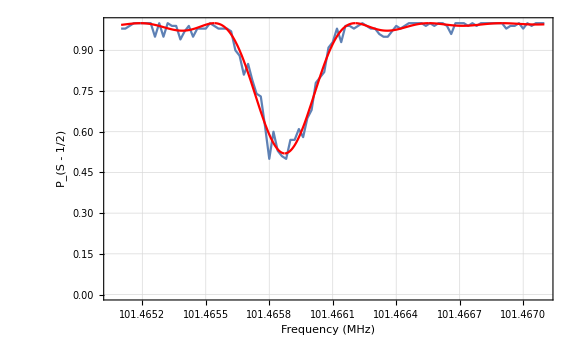
{0.143822,{101.466,FittedModel[1.-(7.00218×10^-9 Sin[9145.24 √(«22»+(«1»)^(«3»))]^2.)/(7.00218×10^-9+(-101.466+x)^2.)],{ | Estimate | Standard Error | Confidence Interval
α | -0.000083679 | 1.09588×10^-6 | {-0.0000858538,-0.0000815043}
β | 101.466 | 2.16549×10^-6 | {101.466,101.466}
γ | 2911.02 | 42.8569 | {2825.97,2996.07},-Graphics-}}}

```mathematica
(*fit!*)
fittedSincData=AbsoluteTiming[
fitSinc[datasetProcessed,timeReadoutUS]
]
```

## Show

```mathematica
NumberForm[fittedSincData[[2,1]],9]
fittedSincData[[2,3]]//MatrixForm
```

101.465873

( | Estimate | Standard Error | Confidence Interval
α | -0.000083679 | 1.09588×10^-6 | {-0.0000858538,-0.0000815043}
β | 101.466 | 2.16549×10^-6 | {101.466,101.466}
γ | 2911.02 | 42.8569 | {2825.97,2996.07}
-Graphics-)

## laser scan - sinc fit

```mathematica
mzdp0={
{1.,1953.1},
{1.5,2833.48},
{2.,3764.71},
{2.5,4429.33},
{3.,5027.11}, 
{3.5,5587.2},
{4.,3692.37},
{4.5,2532.7},
{5.,2723.18}
};
mzdp0[[;;,2]]*=0.5*(1.*^0  );
```

```mathematica
mzdp1={    
{1.,0.},
{1.5,0.},
{2.,0.},  
{2.5,4507.98}, 
{3.,5542.77},
{3.5,6308.86},
{4.,0.},
{4.5,0.},
{5.,2584.3}
};
mzdp1[[;;,2]]*=0.5*(1.*^0);
```

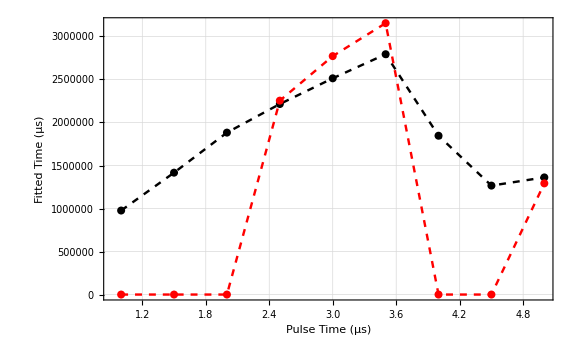

```mathematica
ListLinePlot[
{
mzdp0, 
mzdp0,
mzdp1,
mzdp1
},
FrameLabel->{ 
{Style["Fitted Time (μs)",{Black,Directive[15]}],None},
{
Style["Pulse Time (μs)",{Black,Directive[15]}],
Style["Laser Scan Coherence (Untriggered)",{Black,Directive[15]}]
}
},
PlotStyle->{ 
{Black,PointSize[0.01]},{Black,Dashed,Thickness[0.003]},
{Red,PointSize[0.01]},{Red,Dashed,Thickness[0.003]} 
},
Joined->{False,True,False,True}
]
```

## EGGS time series view

```mathematica
rid=74381;
```

```mathematica
freqInterestHz=84.2000*(1.*^6);
```

### Import

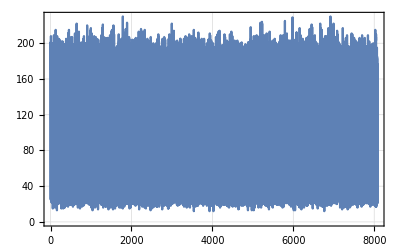
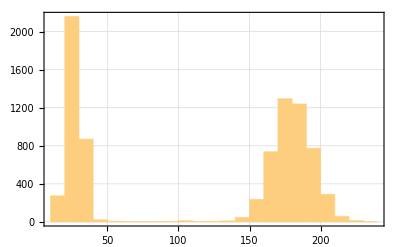

```mathematica
datafile=ImportDatasetARTIQ[directoryString,ToString[#]]&[rid];
{dataset,parameters}=datafile;
{ListLinePlot[#[[;;]],PlotRange->Full,ImageSize->Scaled[0.3]],Histogram[#,ImageSize->Scaled[0.3]]}&[dataset[[;;,2]]]
{
(*todo: params*)
};
```

```mathematica
dataset[[;;3]]//MatrixForm
```

(4.34084×10^8 | 173. | 8.386×10^7 | 1.39829×10^6 | 0. | 266999.
4.40073×10^8 | 201. | 8.386×10^7 | 1.39829×10^6 | 0. | 266999.
4.34084×10^8 | 168. | 8.386×10^7 | 1.39829×10^6 | 0. | 266999.)

### Process

```mathematica
(*process dataset*)
datasetProcessed=ThresholdCounts[dataset[[;;,{1,3,2}]],3];
datasetProcessed=Transpose[Transpose[datasetProcessed]*{ftwToFrequencyMHz,1.,1}];
freqCenter=Mean[datasetProcessed[[;;,1]]];
(*get min and max EGGS freqs*)
eggsMinFreqHz=Min[datasetProcessed[[;;,2]]];
eggsMaxFreqHz=Max[datasetProcessed[[;;,2]]];
```

```mathematica
(*process rsb and bsb*)
dsR=Select[datasetProcessed,#[[1]]<freqCenter&][[;;,{2,3}]];
dsB=Select[datasetProcessed,#[[1]]>=freqCenter&][[;;,{2,3}]];
dsR=Values[CollateData[dsR,{1}]];
dsB=Values[CollateData[dsB,{1}]];
(*sort*)
dsR=SortBy[dsR,First];
dsB=SortBy[dsB,First];
```

```mathematica
(*process phonon number*)
dsRatio=dsR;
dsRatio[[;;,2]]/=dsB[[;;,2]];
dsN=dsRatio;
dsN[[;;,2]]=CoherentC[dsN[[;;,2]]];
```

### Get Peak Time-Series

```mathematica
(*create association with keys as indices for convenience*)
dsTimeSeries=AssociationThread[Range[Length[datasetProcessed]]->datasetProcessed];
```

```mathematica
(*get generalized red and blue for comparison*)
timeSeriesGeneralRed=Select[
dsTimeSeries,
(#[[1]]<freqCenter)&
][[;;;;7]];
timeSeriesGeneralRed=Transpose[{
Keys[timeSeriesGeneralRed],
#[[3]]&/@Values[timeSeriesGeneralRed]
}];

timeSeriesGeneralBlue=Select[
dsTimeSeries,
(#[[1]]>freqCenter)&
][[;;;;10]];
timeSeriesGeneralBlue=Transpose[{
Keys[timeSeriesGeneralBlue],
#[[3]]&/@Values[timeSeriesGeneralBlue]
}];
```

```mathematica
(*get red time series with indices as x-axis (i.e. don't assume contiguous)*)
timeSeriesInterestRed=Select[
dsTimeSeries,
(#[[1]]<freqCenter)&&(Abs[#[[2]]-freqInterestHz]<80.)&
];
timeSeriesInterestRed=Transpose[{
Keys[timeSeriesInterestRed],
#[[3]]&/@Values[timeSeriesInterestRed]
}];
```

```mathematica
(*get blue time series with indices as x-axis (i.e. don't assume contiguous)*)
timeSeriesInterestBlue=Select[
dsTimeSeries,
(#[[1]]>freqCenter)&&(Abs[#[[2]]-freqInterestHz]<80.)&
];
timeSeriesInterestBlue=Transpose[{
Keys[timeSeriesInterestBlue],
#[[3]]&/@Values[timeSeriesInterestBlue]
}];
```

### Plot

```mathematica
(*plot time series of R/B points for GENERAL points*)
timeSeriesGeneralPlot={
ListPlot[
{
timeSeriesGeneralRed,
timeSeriesGeneralRed
},
Joined->{False,True},
PlotStyle->{
{Red,PointSize[0.01]},
{Red,Thickness[0.003],Dashed}
},
FrameLabel->{ 
{Style["D-State Probability (P_(↑.))",{Black,Directive[15]}],None},
{
Style["Relative Time (arb.)",{Black,Directive[15]}],
Style["EGGS Scan (RSB) - General \nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
],
ListPlot[
{
timeSeriesGeneralBlue,
timeSeriesGeneralBlue
},
Joined->{False,True},
PlotStyle->{
{Blue,PointSize[0.01]},
{Blue,Thickness[0.003],Dashed}
},
FrameLabel->{ 
{Style["D-State Probability (P_(↑.))",{Black,Directive[15]}],None},
{
Style["Relative Time (arb.)",{Black,Directive[15]}],
Style["EGGS Scan (RSB) - General \nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
]
};
```

```mathematica
(*plot time series of R/B points for frequency of interest*)
timeSeriesInterestPlot={
ListPlot[
{
timeSeriesInterestRed,
timeSeriesInterestRed
},
Joined->{False,True},
PlotStyle->{
{Red,PointSize[0.01]},
{Red,Thickness[0.003],Dashed}
},
FrameLabel->{ 
{Style["D-State Probability (P_(↑.))",{Black,Directive[15]}],None},
{
Style["Relative Time (arb.)",{Black,Directive[15]}],
Style["EGGS Scan (RSB) @ "<>ToString[freqInterestHz/(1.*^6)]<>" MHz \nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
],
ListPlot[
{
timeSeriesInterestBlue,
timeSeriesInterestBlue
},
Joined->{False,True},
PlotStyle->{
{Blue,PointSize[0.01]},
{Blue,Thickness[0.003],Dashed}
},
FrameLabel->{ 
{Style["D-State Probability (P_(↑.))",{Black,Directive[15]}],None},
{
Style["Relative Time (arb.)",{Black,Directive[15]}],
Style["EGGS Scan (BSB) @ "<>ToString[freqInterestHz/(1.*^6)]<>" MHz \nRID: "<>ToString[rid],{Black,Directive[15]}]
}
}
]
};
```

```mathematica
(*plot EGGS summary figure*)
summaryFigure={
ListPlot[
{
dsR,
dsB
},
PlotRange->{Automatic,{0.,1.}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["EGGS Freq. (Hz)",{Black,Directive[15]}],
Style["EGGS Scan ("<>ToString[eggsMinFreqHz/(1.*^6)]<>" - "<>ToString[eggsMaxFreqHz/(1.*^6)]<>") MHz = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Red,Blue,Black}
],
Show[
ListPlot[
{dsN},
(*PlotRange->{Automatic,{0.,1.}},*)
PlotRange->{Automatic,{0.,Full}},
FrameLabel->{ 
{Style["⟨n⟩",{Black,Directive[15]}],None},
{
Style["EGGS Freq. (Hz)",{Black,Directive[15]}],
Style["EGGS Scan ("<>ToString[eggsMinFreqHz/(1.*^6)]<>" - "<>ToString[eggsMaxFreqHz/(1.*^6)]<>") MHz = "<>ToString[First[parameters["time_delay_us_list"]]]<>" μs)\nRID: "<>ToString[rid],{Black,Directive[15]}]
}
},
PlotStyle->{Black}
](*,
fitPlot*)
]
};
```

### Show

```mathematica
First@dsN[[Ordering[dsN[[;;,2]],-1],1]]
```

8.396×10^7

```mathematica
8.396*^7
```

8.396×10^7

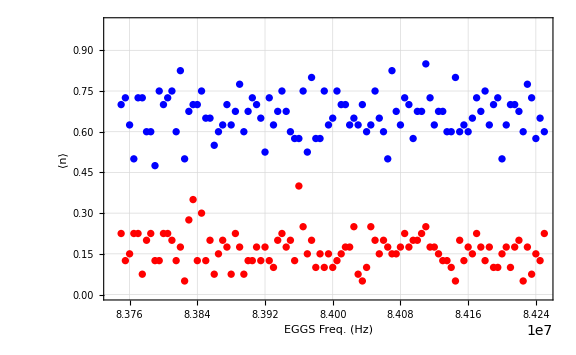
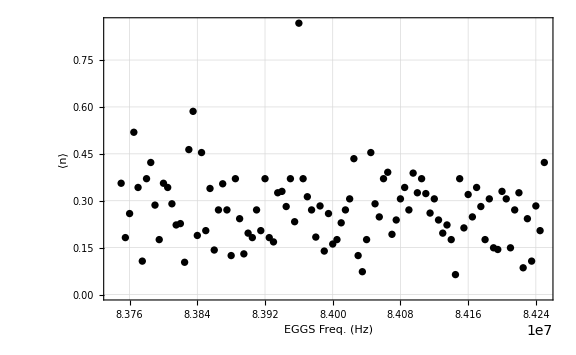

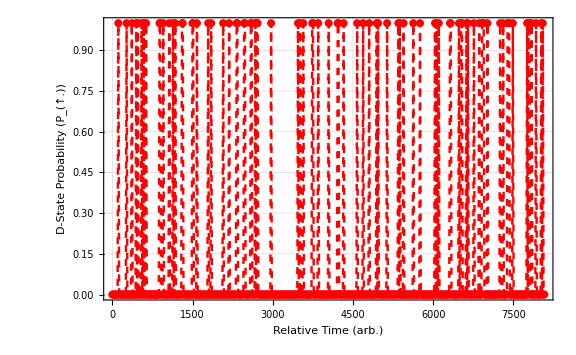
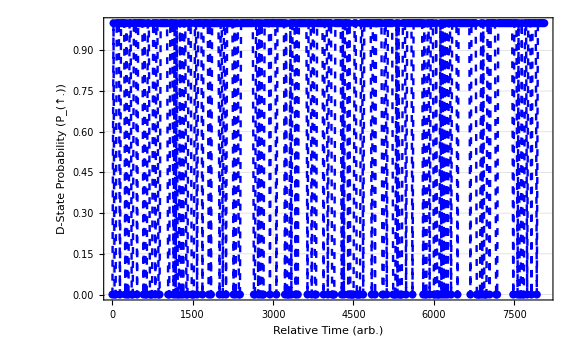

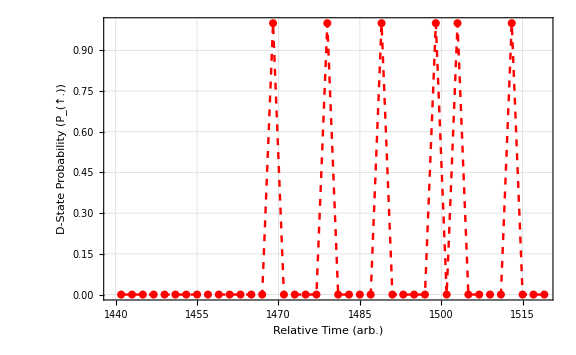
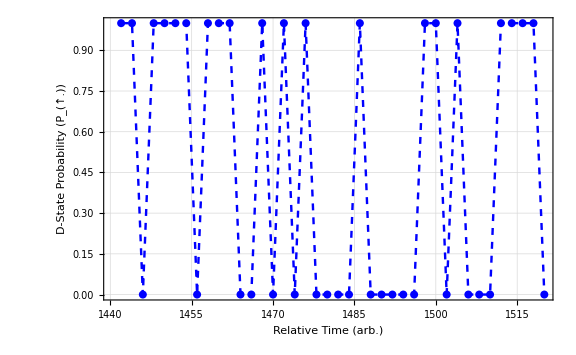

```mathematica
summaryFigure
timeSeriesGeneralPlot
timeSeriesInterestPlot
```

### fd